論文とnotebookの軸名 / Axis names in the manuscript and notebook

論文の Front と Back は，この notebook ではそれぞれ In と Out と呼ぶ．したがって，論文の Back–Front 軸は notebook の Out–In 軸に対応する．
In this notebook, the manuscript’s Front and Back are labeled In and Out, respectively. Thus, the manuscript’s Back–Front axis corresponds to the notebook’s Out–In axis.

Front（manuscript）= In（this notebook）
Back（ manuscript）= Out（this notebook）

```mathematica
(*Notebookを置いたフォルダーの親フォルダーを プロジェクトの基準フォルダーとして使用する Use the parent of the notebook directory as the project root*)
baseDir=DirectoryName[NotebookDirectory[]];

(*後続コードで使用するデータフォルダー Data directories used by the subsequent code*)
dir=baseDir;
dirw=FileNameJoin[{baseDir,"VAE_weight_Eng3D"}]<>$PathnameSeparator;
dir1=FileNameJoin[{baseDir,"shapeddata"}]<>$PathnameSeparator;
```

```mathematica
(*必要なフォルダーが存在することを確認する Verify that the required directories exist*)
<|"ProjectDirectory"->DirectoryQ[dir],"VAEWeightDirectory"->DirectoryQ[dirw],"ShapedDataDirectory"->DirectoryQ[dir1]|>
```

<|ProjectDirectory→True,VAEWeightDirectory→True,ShapedDataDirectory→True|>

```mathematica
cl= ColorData["DefaultPlotColors","ColorList"];
```

```mathematica
(*CSVの第1列をバイアス，残りの列を重み行列として読み込む 
Import the first CSV column as the bias vector and the remaining columns as the weight matrix*)importVAEParameters[file_String]:=Module[{table},table=Import[FileNameJoin[{dirw,file}],"CSV"];
{Transpose[table[[2;;,2;;]]],table[[2;;,1]]}];

(*学習済みEncoderとDecoderのパラメータを読み込む Import the trained Encoder and Decoder parameters*)
{wedE,wedbE}=importVAEParameters["VAEweD_eng3D20240411.csv"];
{wezmE,wezmbE}=importVAEParameters["VAEweZm_eng3D20240411.csv"];
{wezlvE,wezlvbE}=importVAEParameters["VAEweZlv_eng3D20240411.csv"];
{wdd1E,wdd1bE}=importVAEParameters["VAEwdD1_eng3D20240411.csv"];
{wdd2E,wdd2bE}=importVAEParameters["VAEwdD2_eng3D20240411.csv"];
```

```mathematica
(*CDIデータをヘッダー行を含めて読み込む．参加者情報の列（data_id，child_id，age）は，科学表記を含む文字列として 読み込まれる場合があるため整数に変換する．その後，CDI応答を0/1に変換し，ヘッダー行を保持したalldataを作成する．Import the CDI data while retaining the header row.Because the participant-information columns (data_id，child_id，and age) may be imported as strings，including scientific notation，convert them to integers.Then convert the CDI responses to 0/1 and construct alldata while preserving the header row.*)
raw=Import[FileNameJoin[{dir1,"EnglishAmerican_WS_20240411_shaped_wide.csv"}],"CSV","HeaderLines"->0];
toInteger[s_String]:=Module[{p},p=StringSplit[ToLowerCase[StringTrim[s]],"e"];
If[Length[p]==2,Round[ToExpression[p[[1]]]*10^ToExpression[p[[2]]]],Round[ToExpression[s]]]];
raw[[2;;,2;;4]]=Map[toInteger,raw[[2;;,2;;4]],{2}];
alldata=Prepend[Rest[raw]/. {""->0,"produces"->1,"NA"->0,Missing[_]->0},First[raw]];
```

```mathematica
(*alldataから680項目のCDI応答行列を抽出する 
Extract the 680-item CDI response matrix from alldata*)data=alldata[[2;;,5;;]];
```

```mathematica
dataitem= Import[FileNameJoin[{dir1,"english_cdi_word_category_symbol_mapping.xls"}],"xls"][[1]];
```

```mathematica
debRoy3D=Import[FileNameJoin[{dir1,"characterlist3D20240411.xlsx"}],"xlsx"][[1]];
```

```mathematica
(*SAYCamの縦断語彙データを読み込み，先頭の7行を除いて 空欄を未産出の0に変換する．
Import the SAYCam longitudinal vocabulary data，remove the first seven rows，and convert blank responses to 0 for not produced．*)dataSAYtmp=Import[FileNameJoin[{dir,"SAYCam","EnglishAmerican_WS_SAYCam_wide.xlsx"}],"xlsx"][[1]];
dataSAY=dataSAYtmp[[8;;]]/. {""->0};
```

#### EncoderによるCDIプロフィールの3次元潜在表現の計算 Encoding CDI profiles into the three-dimensional latent space

```mathematica
d=Length[data[[1]]]
```

680

```mathematica
relu[x_]:=Max[0,x]
```

```mathematica
Dimensions/@{data,wedE,wedbE}
```

{{9093,680},{680,512},{512}}

```mathematica
biasz=ConstantArray[wedbE,Length[data]];
```

```mathematica
denseE=Map[relu,data.wedE+biasz,{2}];
```

```mathematica
Dimensions[denseE]
```

{9093,512}

#### 行列演算による潜在平均と対数分散の一括計算 Batched computation of latent means and log variances using matrix operations

```mathematica
(*各CDIプロフィールを個別に取り出して計算する代わりに，全プロフィールを行列として一括処理することで，Encoderの潜在平均と対数分散を効率よく計算する．
Rather than processing CDI profiles one at a time，compute the latent means and log variances efficiently by applying the Encoder to all profiles as matrix operations.*)
```

```mathematica
Dimensions /@{denseE,wezmE,wezmbE}
```

{{9093,512},{512,3},{3}}

```mathematica
calcZ[dense_,wez_,wezb_]:= Module[{dummy,bias,zdata},
dummy= dense.wez;
bias=ConstantArray[wezb,Length[data]];
zdata= dummy+ bias;
zdata
]
```

```mathematica
zdataE0=calcZ[denseE,wezmE, wezmbE];
```

```mathematica
lσdataE0=calcZ[denseE,wezlvE,wezlvbE];
```

```mathematica
Dimensions/@{zdataE0,lσdataE0}
```

{{9093,3},{9093,3}}

```mathematica
(*軸反転前の潜在座標系で使用するEncoderとDecoderを定義する．後で定義するtozとpredictは，revmによる軸反転後の座標系を使用する．Define the Encoder and Decoder in the original latent coordinate system.The later toz and predict use coordinates after the axis transformation by revm.*)
```

```mathematica
toz0[x_]:=Module[{de,a},
de=relu[#]&/@(x.wedE+wedbE);
a=de.wezmE+wezmbE;
a
]
```

```mathematica
tologsigma0[x_]:=Module[{de,a},
de=relu[#]&/@(x.wedE+wedbE);
a=de.wezlvE+wezlvbE;
a
]
```

```mathematica
predictorg[z_]:=LogisticSigmoid[((relu[#]&/@((z.wdd1E)+wdd1bE)).wdd2E+wdd2bE)]
```

#### 事前計算したDecoder出力グリッドの読み込み Import of the precomputed decoder output grid

```mathematica
decallorg=Import[FileNameJoin[{dirw,"VAEdecAlleng3D20240411.csv"}],"csv"];
decallorg=ArrayReshape[decallorg,{680,30,30,30}];
```

#### 潜在座標系の軸反転 Reflection of the latent coordinate axes

```mathematica
(*潜在座標の第2・第3軸を反転する．分散に対応する成分は 軸の符号反転によって変化しない．Reverse the second and third latent axes.The corresponding variance components are unchanged by these sign reversals.*)
```

```mathematica
revm={{1,0,0},{0,-1,0},{0,0,-1}};
```

```mathematica
revmσ = Abs[revm]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
(*読み込んだ全CDIプロフィールの潜在平均座標zdataE0に 軸反転を適用し，zdataEを作成する．Apply the axis reflection to the latent mean coordinates zdataE0 of all imported CDI profiles to obtain zdataE.*)
```

```mathematica
zdataE=revm.# &/@zdataE0;
```

```mathematica
lσdataE=lσdataE0;
```

```mathematica
(*任意の1件の680項目CDIプロフィールを入力し，軸反転後の3次元潜在平均座標を返す関数．Function that takes one arbitrary 680-item CDI profile and returns its three-dimensional latent mean in the reflected coordinate system.*)
```

```mathematica
toz[x_]:=Module[{de,a},
de=relu[#]&/@(x.wedE+wedbE);
a=de.wezmE+wezmbE;
revm.a
]
```

```mathematica
(*任意の1件の680項目CDIプロフィールを入力し，軸反転後の各潜在軸に対応する対数分散を返す関数．軸の符号反転によって分散の値は変わらない．Function that takes one arbitrary 680-item CDI profile and returns the log variance for each reflected latent axis.Reversing an axis does not change its variance.*)
```

```mathematica
tologsigma[x_]:=Module[{de,a},
de=relu[#]&/@(x.wedE+wedbE);
a=de.wezlvE+wezlvbE;
revmσ.a
]
```

#### 潜在空間における総語彙割合グリッドの構築 Constructing the total vocabulary proportion grid in latent space

```mathematica
(*事前計算したDecoder出力の格子点に，軸反転後の座標を対応づける．各点で680語の産出確率を平均し，{z1,z2,z3,総語彙割合} の形式でgridallを作成する．Associate the precomputed decoder grid with coordinates after axis reflection.At each point,average the production probabilities across 680 words to construct gridall as {z1,z2,z3,total vocabulary proportion}.*)
```

```mathematica
grid=Table[revm.{i,j,k},{i,-4,4,8/29//N},{j,4,-4,-8/29//N},{k,4,-4,-8/29//N}];
```

```mathematica
decall=decallorg;
```

```mathematica
gridall=Flatten[Table[{grid[[i,j,k]],Mean[decall[[;;,i,j,k]]]}//Flatten,{i,1,30},{j,1,30},{k,1,30}],2];
```

#### CDIプロフィールと全0・全1プロフィールの潜在空間上の位置 Latent positions of CDI profiles and the all-zero and all-one profiles

```mathematica
pz=Show[
ListPointPlot3D[zdataE,BoxRatios->1,PlotRange->{{-4,4},{-4,4},{-4,4}},PlotStyle->PointSize[0.006],AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},ViewPoint->{1.0,-3,1}],
Graphics3D[{PointSize[0.03],Point[toz[Table[0,d]]]}],
Graphics3D[{Red,PointSize[0.03],Point[toz[Table[1,d]]]}]
]
```

-Graphics3D-

```mathematica
predict[z_]:=LogisticSigmoid[((relu[#]&/@(((revm.z).wdd1E)+wdd1bE)).wdd2E+wdd2bE)]
```

#### 事前計算した等総語彙割合面の独立検算 Independent validation of the precomputed total vocabulary isosurface

```mathematica
(*高密度の格子全体をMathematicaのpredictで直接計算すると時間がかかるため，通常の等総語彙割合面にはColabで事前計算したDecoder出力を使用する．ここでは粗い9×9×9格子でpredictを直接評価してmpfuncを作り，その0.5等値面cmp05をCSV由来のcmp05Gridと重ねて形状を比較する．Direct evaluation of predict on a dense grid is time-consuming.The main isosurface therefore uses decoder outputs precomputed in Colab.Here,mpfunc is constructed from direct predictions on a coarse 9×9×9 grid,and its 0.5 isosurface (cmp05) is overlaid with the CSV-based isosurface (cmp05Grid) for a visual comparison.*)
```

```mathematica
mpdata=Table[{{x,y,z},Mean[predict[{x,y,z}]]},{x,-4,4,1},{y,-4,4,1},{z,-4,4,1}];
```

```mathematica
mpfunc=Interpolation[Flatten[mpdata,2]];
```

```mathematica
cmp05=ContourPlot3D[mpfunc[x,y,z]==0.5,{x,-4,4},{y,-4,4},{z,-4,4},ContourStyle->Opacity[0.5],AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]}]
```

-Graphics3D-

```mathematica
cmp05Grid=ListContourPlot3D[gridall,Contours->0.5,ContourStyle->{cl[[2]],Opacity[0.5]},AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},PlotRange->{{-4,4},{-4,4},{-4,4}}]
```

-Graphics3D-

```mathematica
(*事前計算したdecall由来の0.5等値面と，predictを直接評価して 補間した0.5等値面を重ね，形状がほぼ一致することを確認する．Overlay the 0.5 isosurfaces derived from precomputed decall values and direct predict evaluations to check their close visual agreement.*)
```

```mathematica
Show[cmp05Grid,cmp05]
```

-Graphics3D-

```mathematica
Show[pz,cmp05Grid]
```

-Graphics3D-

```mathematica
cmp020508Grid=ListContourPlot3D[gridall,Contours->{0.2,0.5,0.8},ContourStyle->Opacity[0.5],AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},PlotRange->{{-4,4},{-4,4},{-4,4}}]
```

-Graphics3D-

```mathematica
Show[pz,cmp020508Grid]
```

-Graphics3D-

#### CDI 680項目の語・カテゴリー情報の整理 Organizing word and category information for the 680 CDI items

```mathematica
(*各項目にカテゴリー名を補完する Fill in the category name for every item*)itemCategories=Rest@FoldList[If[#2==="",#1,#2]&,"",dataitem[[All,1]]];

(*項目表を {項目番号,カテゴリー,語,CDIコード} の形式にする Construct the item table as {item number,category,word,CDI code}*)
dataitem3=Transpose[{Range[Length[dataitem]],itemCategories,dataitem[[All,2]],dataitem[[All,3]]}];

(*項目番号から項目情報を検索するための対応表 Lookup table from item number to item information*)
itemByNumber=AssociationThread[dataitem3[[All,1]],dataitem3];

(*項目番号nから{項目番号，カテゴリー名，語，CDIコード}を取得する．登録されていない番号にはMissingを返す．Look up item number n and return {item number,category,word,CDI code}.Return Missing if the number is not registered.*)
fitem3[n_Integer]:=Lookup[itemByNumber,n,Missing["UnknownItemNumber",n]];

(*元の順序を保ったカテゴリー名一覧 Category names in their original order*)
catname=DeleteDuplicates[itemCategories];

(*カテゴリーごとに項目をまとめる Group the items by category*)
categoryRows=Lookup[GroupBy[dataitem3,#[[2]]&],catname];

(*各カテゴリーに含まれる項目数 Number of items in each category*)
numitems=Length/@categoryRows;

(*各カテゴリーの項目番号範囲 Item-number range for each category*)
catn=MinMax/@categoryRows[[All,All,1]];

(*{カテゴリー番号,カテゴリー名,項目数} の要約表 Summary table:{category number,category name,number of items}*)
catnumitems=Transpose[{Range[Length[catname]],catname,numitems}];
```

```mathematica
fitem3[401]
```

{401,n-action_words,bite,n1}

```mathematica
cols={"no","22分類","語彙数"};
```

```mathematica
Grid[Prepend[catnumitems[[1;;-1]],cols],Frame->All,Alignment->Left]
```

no | 22分類 | 語彙数
1 | a-sounds | 12
2 | b-animals | 43
3 | c-vehicles | 14
4 | d-toys | 18
5 | e-food_drink | 68
6 | f-clothing | 28
7 | g-body_parts | 27
8 | h-household | 50
9 | i-furniture_rooms | 33
10 | j-outside | 31
11 | k-places | 22
12 | l-people | 29
13 | m-games_routines | 25
14 | n-action_words | 103
15 | o-descriptive_words | 63
16 | p-time_words | 12
17 | q-pronouns | 25
18 | r-question_words | 7
19 | s-locations | 26
20 | t-quantifiers | 17
21 | u-helping_verbs | 21
22 | v-connecting_words | 6

```mathematica
Grid[Prepend[catnumitems[[1;;11]],cols],Frame->All,Alignment->Left];
```

```mathematica
Grid[Prepend[catnumitems[[12;;-1]],cols],Frame->All,Alignment->Left];
```

#### 総語彙数によるCDIデータと潜在座標の並べ替え Ordering CDI profiles and latent coordinates by total vocabulary size

```mathematica
(*各参加者の総語彙数 Total vocabulary size for each participant.*)
vocabularyTotals=Total/@alldata[[2;;,5;;]];

(*元のコードと同じ方法で総語彙数順を求める Determine the vocabulary-size order using the original method.*)
vocabularyOrder=Sort[Transpose[{Range[Length[vocabularyTotals]],vocabularyTotals}],#1[[2]]<#2[[2]]&][[All,1]];

(*潜在空間データを元のコードと同じ順序で並べ替える Reorder the latent-space data in the same order as the original code.*)
zdataEsort=zdataE[[vocabularyOrder]];
lσdataEsort=lσdataE[[vocabularyOrder]];
```

```mathematica
(*CDIデータも潜在座標と同じ参加者順に並べ，見出し行を先頭に戻す．Reorder CDI rows to match the latent coordinates and retain the header as the first row.*)alldatasort=Prepend[alldata[[1+vocabularyOrder]],First[alldata]];
```

```mathematica
(*同じ順序に並べた各参加者の総語彙数．Total vocabulary sizes in the same participant order.*)totlist=vocabularyTotals[[vocabularyOrder]];
```

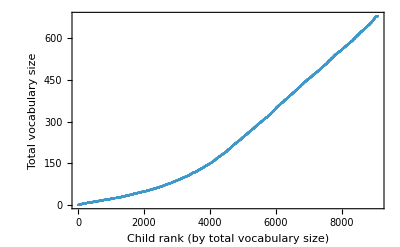

```mathematica
ListPlot[totlist,Frame->True,FrameLabel->{"Child rank (by total vocabulary size)","Total vocabulary size"},FrameStyle->14]
```

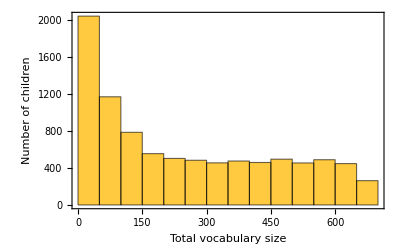

```mathematica
Histogram[totlist,Frame->True,FrameLabel->{"Total vocabulary size","Number of children"},FrameStyle->14]
```

#### 潜在空間のゆらぎを描画 , Encoder事後分布の不確実性 Uncertainty of the encoder posterior distributions

```mathematica
zAllZero=toz[ConstantArray[0,d]];
zAllOne=toz[ConstantArray[1,d]];
```

```mathematica
(*CDIプロファイルを潜在座標の平均と事後標準偏差で表す 
Represent a CDI profile by latent-coordinate means and posterior standard deviations*)ardata[x_]:=MapThread[Around,{toz[x],Exp[0.5*tologsigma[x]]}];
```

```mathematica
(*潜在空間の点群と全語未獲得・全語獲得プロファイルの位置 
Latent-space point cloud and the locations of the all-zero and all-one vocabulary profiles*)latentSpaceReferencePlot=Show[ListPointPlot3D[zdataE,BoxRatios->1,PlotRange->{{-4,4},{-4,4},{-4,4}},PlotStyle->PointSize[0.003],AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},ViewPoint->{1.0,-3,1}],Graphics3D[{PointSize[0.03],Point[zAllZero]}],Graphics3D[{Red,PointSize[0.03],Point[zAllOne]}]];
```

```mathematica
(*総語彙数で並べたデータから，発達段階の異なる例を選択する 
Select examples at different developmental stages from the data ordered by total vocabulary size*)posteriorExampleRanks={400,1010,2030,4020,6150,7010,8150,8800};

posteriorExampleProfiles=Join[{ConstantArray[0,d],ConstantArray[1,d]},alldatasort[[posteriorExampleRanks+1,5;;]]];

posteriorExamples=ardata/@posteriorExampleProfiles;
```

```mathematica
(*点は事後平均，誤差線は各潜在次元の±1標準偏差を表す 
Points indicate posterior means，and error bars indicate±1 standard deviation along each latent dimension*)posteriorUncertaintyPlot=Show[latentSpaceReferencePlot,ListPointPlot3D[posteriorExamples,PlotStyle->Directive[Red,PointSize[0.01],Thickness[0.003]]],ImageSize->500]
```

-Graphics3D-

#### 語彙数ランキングでプロット 動画作成も含む total vocabulary size (ascending order)

```mathematica
pzt=Show[
ListPointPlot3D[zdataE,BoxRatios->1,PlotRange->{{-4,4},{-4,4},{-4,4}},PlotStyle->PointSize[0.003],AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},ViewPoint->{1.0,-3,1},
PlotLabel->Style["total vocabulary size (ascending order)",16]],
Graphics3D[{PointSize[0.03],Point[toz[Table[0,d]]]}],
Graphics3D[{Red,PointSize[0.03],Point[toz[Table[1,d]]]}]
]
```

-Graphics3D-

```mathematica
no1=101;no2=no1+20;Show[pzt,ListPointPlot3D[zdataEsort[[no1;;no2]],AspectRatio->1,PlotRange->{{-4,4},{-4,4},{-4,4}},PlotStyle->{Magenta,PointSize[0.012]}]];
```

```mathematica
no1=500;no2=no1+10;
voc1=Total[alldatasort[[no1+1,5;;]]];
voc2=Total[alldatasort[[no2+1,5;;]]];
Show[pzt,ListPointPlot3D[zdataEsort[[no1;;no2]],AspectRatio->1,PlotRange->{{-4,4},{-4,4},{-4,4}},PlotStyle->{Magenta,PointSize[0.018]}],Graphics3D[Text[TextGrid[{{Style["ranking",14],Style[no1,14],Style["~",14],Style[no2,14]}}],{-2.5,-2,-3.3}]],
Graphics3D[Text[TextGrid[{{Style["voc",14],Style[voc1,14],Style["~",14],Style[voc2,14]}}],{-2.5,-2,-4.}]]]
```

-Graphics3D-

```mathematica
(*Generate movie frames for successive groups of 10 participants,ranked by total vocabulary size in ascending order.Each frame highlights one group in magenta and shows its rank and vocabulary-size ranges.*)
```

```mathematica
(*
mv1=Table[no1=k;no2=no1+9;
voc1=Total[alldatasort[[no1+1,5;;]]];
voc2=Total[alldatasort[[no2+1,5;;]]];
Show[pzt,ListPointPlot3D[zdataEsort[[no1;;no2]],AspectRatio->1,PlotRange->{{-4,4},{-4,4},{-4,4}},PlotStyle->{Magenta,PointSize[0.018]}],Graphics3D[Text[TextGrid[{{Style["ranking",14],Style[no1,14],Style["~",14],Style[no2,14]}}],{-2.5,-2,-3.3}]],
Graphics3D[Text[TextGrid[{{Style["voc",14],Style[voc1,14],Style["~",14],Style[voc2,14]}}],{-2.5,-2,-4}]]],
{k,1,Length[data]-10,10}];
*)
```

```mathematica
(* mvout=ListAnimate[mv1]*)
```

```mathematica
(* Export["voc-eng3d-reconst-rank.mp4",mvout]*)
```

```mathematica
(* frame-by-frame export by png  *)
```

```mathematica
(*Supplementary movie:frame-by-frame export ListAnimate[mv1] is used only for preview.During interactive playback,intermediate frames may be skipped if rendering cannot keep up.For the supplementary movie,each element of mv1 is exported as a numbered PNG using the loop below.The PNG sequence is then assembled into an MP4 file with FFmpeg.Before encoding,verify that the number of PNG files equals Length[mv1],the frame numbers are consecutive,and all images have the same dimensions.The current outdir is a filename prefix:D:\work\output\test It produces test000001.png,test000002.png,etc.Example command to run from D:\work\output (12 frames per second):ffmpeg-framerate 12-start_number 1-i "test%06d.png"-c:v libx264-pix_fmt yuv420p "voc-eng3d-reconst-rank.mp4"*)
```

```mathematica
(* filenumber[frame_]:=Floor[frame/dframe]*)
filenumber[frame_]:=frame
outdir="D:"<>"\\work\\output\\test";
```

```mathematica
(* ft=100;Export[outdir<>IntegerString[filenumber[ft],10,6]<>".png",mv1[[ft]]]*)
```

```mathematica
(* Do[Export[outdir<>IntegerString[filenumber[frame],10,6]<>".png",mv1[[frame]]],{frame,1,Length[mv1],1}];*)
```

```mathematica
(**)
```

#### 総語彙数に基づく平均発達曲線 Mean developmental trajectory based on total vocabulary size

```mathematica
k=2000;Show[
ListPointPlot3D[zdataE,BoxRatios->1,PlotRange->{{-4,4},{-4,4},{-4,4}},PlotStyle->PointSize[0.0035],AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},ViewPoint->{1.0,-3,1}],
Graphics3D[{PointSize[0.03],Point[toz[Table[0,d]]]}],
Graphics3D[{Red,PointSize[0.03],Point[toz[Table[1,d]]]}],
ListPointPlot3D[zdataEsort[[k+1;;k+100]],AspectRatio->1,PlotStyle->Green]
]
```

-Graphics3D-

```mathematica
(*
子どもを総語彙数の昇順に並べ，300名の移動窓（移動幅100名）ごとに
zdata の平均を計算した．得られた平均潜在座標の系列を
「平均発達曲線」と呼ぶ．
Children were ordered by total vocabulary size,and mean zdata was
calculated using overlapping windows of 300 children with a step size
of 100. The resulting sequence of mean latent coordinates is referred
to as the mean developmental trajectory.
*)
```

```mathematica
nz=300;dnz=100;
```

```mathematica
meanzdataE=Mean[#]&/@Partition[zdataEsort,nz,dnz];
```

```mathematica
Show[
ListPointPlot3D[zdataE,BoxRatios->1,PlotRange->{{-4,4},{-4,4},{-4,4}},PlotStyle->PointSize[0.0035],AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},ViewPoint->{1.0,-3,1}],
Graphics3D[{PointSize[0.03],Point[toz[Table[0,d]]]}],
Graphics3D[{Red,PointSize[0.03],Point[toz[Table[1,d]]]}],
ListPointPlot3D[meanzdataE,AspectRatio->1,PlotStyle->Green],ImageSize->500
]
```

-Graphics3D-

#### 擬一次元構造の論文用図その1 Fig.1a

```mathematica
(*各児の総語彙数と0–1に正規化した値 Total vocabulary size for each child and its normalized value*)vocabSize=Total/@alldatasort[[2;;,5;;]];
vocabScore=N[vocabSize/680];

(*潜在座標と語彙データの行数が一致することを確認 Confirm that the latent coordinates and vocabulary data are aligned*)
Assert[Length[zdataEsort]==Length[vocabScore]];
```

```mathematica
Clear[hexColor,lightPurple,basePurple,darkPurple,vocabColor,pointGraphics];

(*16進カラーコードをMathematicaの色に変換する Convert a hexadecimal color code to a Mathematica color*)
hexColor[s_String]:=RGBColor@@(FromDigits[#,16]/255.&/@StringPartition[StringDrop[s,1],2]);

(*総語彙数を表す配色 Color palette representing total vocabulary size*)
lightPurple=RGBColor[40/51,188/255,329/255];
basePurple=hexColor["#7B6FD0"];
darkPurple=hexColor["#2E2257"];

vocabColor[x_]:=Blend[{lightPurple,basePurple,darkPurple},Clip[x,{0,1}]];

(*総語彙数で着色した潜在空間の点群 Latent-space points colored by total vocabulary size*)
pointGraphics=Graphics3D[{PointSize[0.0045],MapThread[{vocabColor[#2],Point[#1]}&,{zdataEsort,vocabScore}]}];
```

```mathematica
(**)
```

```mathematica
legend=BarLegend[{vocabColor,{0,1}},LegendLabel->Style["Total vocabulary size",16],Ticks->{{0.0,"0.0"},{0.2,"0.2  (136 w)"},{0.4,"0.4  (272 w)"},{0.6,"0.6  (408 w)"},{0.8,"0.8  (544 w)"},{1.0,"1.0  (680 w)"}},LabelStyle->Directive[Black,14],LegendMarkerSize->140];

phagi=Legended[Show[pointGraphics,BoxRatios->1,PlotRange->{{-4,4},{-4,4},{-4,4}},Axes->True,AxesLabel->{Style["z1",20,GrayLevel[0.15]],Style["z2",20,GrayLevel[0.15]],Style["z3",20,GrayLevel[0.15]]},TicksStyle->Directive[GrayLevel[0.2],14],AxesStyle->Directive[GrayLevel[0.2],15],BoxStyle->GrayLevel[0.4],ViewPoint->{1.0,-3,1},ImageSize->500],Placed[legend,Right]]
```

-Graphics3D-

```mathematica
(* Export["Fig_1a.cdf",phagi]*)
```

#### 擬一次元構造の論文用図その2 Fig.1b

```mathematica
cnt02=ListContourPlot3D[gridall,Contours->{0.2},ContourStyle->Directive[vocabColor[0.2],Opacity[0.2]],Mesh->None,AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},PlotRange->{{-4,4},{-4,4},{-4,4}}];
```

```mathematica
Show[phagi,cnt02];
```

```mathematica
(* =====Isosurface levels=====*)
levels={0.2,0.4,0.6,0.8};
levelColors=vocabColor/@levels;
surfaceStyles=Directive[#,Opacity[0.25]]&/@levelColors;
```

```mathematica
(* =====Four isosurfaces=====*)cntLevels=ListContourPlot3D[gridall,Contours->levels,ContourStyle->surfaceStyles,Mesh->None,PlotRange->{{-4,4},{-4,4},{-4,4}},BoxRatios->1,Axes->True,Boxed->True,Lighting->"Neutral"];
```

```mathematica
(* =====Legend for the isosurface levels=====*)surfaceLegend=SwatchLegend[levelColors,levels,LegendLabel->Style["Total vocabulary proportion",16],LabelStyle->Directive[Black,14],LegendMarkerSize->{22,14}];
```

```mathematica
(* =====Scatter plot,isosurfaces,and legend=====*)figContour3=Legended[Show[pointGraphics,cntLevels,PlotRange->{{-4,4},{-4,4},{-4,4}},BoxRatios->1,Axes->True,Boxed->True,AxesLabel->{Style["z1",20,GrayLevel[0.15]],Style["z2",20,GrayLevel[0.15]],Style["z3",20,GrayLevel[0.15]]},TicksStyle->Directive[GrayLevel[0.2],14],AxesStyle->Directive[GrayLevel[0.2],15],BoxStyle->GrayLevel[0.4],ViewPoint->{1.0,-3,1},ImageSize->600],Placed[surfaceLegend,Right]];

figContour3
```

-Graphics3D-

```mathematica
(*Export["Fig1_b.cdf",figContour3];*)
```

#### Fig. 1cのための局所発達座標系の構築 Construction of the local developmental coordinate system for Fig. 1c

```mathematica
{nz,dnz}
```

{300,100}

```mathematica
(*総語彙数で並べた潜在座標を重複する局所窓に分割する．Divide the latent coordinates ordered by total vocabulary size into overlapping local windows.*)
```

```mathematica
zp=Partition[zdataEsort,nz,dnz];
```

```mathematica
k=81;Show[esys=Eigensystem[Covariance[zp[[k]]]];
ListPointPlot3D[zdataE,BoxRatios->1,PlotRange->{{-4,4},{-4,4},{-4,4}},PlotStyle->PointSize[0.002],AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},ViewPoint->{1.0,-3,1}],
Graphics3D[{PointSize[0.03],Point[toz[Table[0,d]]]}],
Graphics3D[{Red,PointSize[0.03],Point[toz[Table[1,d]]]}],
ListPointPlot3D[zp[[k]],AspectRatio->1,PlotStyle->{Green,PointSize[0.006]}],
ListPointPlot3D[{Mean[zp[[k]]]},PlotStyle->{{PointSize[0.015],Black}}],
ListPointPlot3D[{Mean[zp[[k]]]+esys[[1,1]]^0.5esys[[2,1]]},PlotStyle->{PointSize[0.015],Orange}],
ListPointPlot3D[{Mean[zp[[k]]]+esys[[1,2]]^0.5esys[[2,2]]},PlotStyle->{PointSize[0.015],Magenta}]
,ImageSize->500
]
```

-Graphics3D-

```mathematica
(*総語彙数で並べた潜在座標を局所窓に分割し，局所PCAを確認する．Divide the latent coordinates ordered by total vocabulary size into local windows and inspect the local PCA.*)
```

```mathematica
center=0.5(toz[Table[0,d]]+toz[Table[1,d]])
```

{1.88959,1.60805,0.903053}

```mathematica
meanfiltervec[vec_,n_]:=Module[{d,work,k},
d = Length[Transpose[vec]];
work= Table[MeanFilter[vec[[All,k]],n],{k,1,d}];
Transpose[work]
]
```

```mathematica
meanfiltervecandend[vec_,n_,m_]:=Module[{d,work,work2,trw,trw2,k},
d = Length[Transpose[vec]];
work2= Table[MeanFilter[vec[[All,k]],2],{k,1,d}];
work= Table[MeanFilter[vec[[All,k]],n],{k,1,d}];
trw2= Transpose[work2];
trw=Transpose[work];
Join[trw2[[1;;m]],trw,trw2[[-m;;-1]]]
]
```

```mathematica
tmp=Append[Mean[#]&/@zp,toz[Table[1,d]]];
```

```mathematica
tmp2 = meanfiltervec[tmp,5];
```

```mathematica
growdirection=Normalize[#]&/@Differences[tmp2];
```

```mathematica
outdirection= Normalize[(# - center)]&/@meanzdataE ;
```

```mathematica
leftdirection=Table[Cross[growdirection[[k]],outdirection[[k]]],{k,1,Length[zp]}];
```

```mathematica
k=1;Show[
ListPointPlot3D[zdataE,BoxRatios->1,PlotRange->{{-4,4},{-4,4},{-4,4}},PlotStyle->PointSize[0.0025],AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},ViewPoint->{1.0,-3,1}],
Graphics3D[{PointSize[0.03],Point[toz[Table[0,d]]]}],
Graphics3D[{Red,PointSize[0.03],Point[toz[Table[1,d]]]}],
Graphics3D[{Thickness[0.004],Arrow[{meanzdataE[[k]],meanzdataE[[k]]+growdirection[[k]]}]}],Graphics3D[{Red,Thickness[0.004],Arrow[{meanzdataE[[k]],meanzdataE[[k]]+outdirection[[k]]}]}],Graphics3D[{Green,Thickness[0.004],Arrow[{meanzdataE[[k]],meanzdataE[[k]]+leftdirection[[k]]}]}],ImageSize->300
]
```

-Graphics3D-

```mathematica
(*局所PCAにより，Center 軌道の周囲に Left，Right，In，Out の4本の軌道を構成する．
Construct the Left,Right,In,and Out trajectories around the Center trajectory using local PCA.*)
```

```mathematica
esyss=Table[Eigensystem[Covariance[zp[[k]]]],{k,1,Length[zp]}];
```

```mathematica
whichvec[vec_,ref_]:=Module[{work,work2},
work=(ref.#)&/@vec;
work2=Sort[Transpose[{Range[Length[work]],work}],Abs[#1[[2]]]>Abs[#2[[2]]]&];
{work2[[1,1]],Sign[work2[[1,2]]]}
]
```

```mathematica
out=Table[whichvec[esyss[[k,2]],outdirection[[k]]],{k,1,Length[zp]}];
```

```mathematica
leftv=Table[whichvec[esyss[[k,2]],leftdirection[[k]]],{k,1,Length[zp]}];
```

```mathematica
k=70;outer2work=meanzdataE[[k]]+2out[[k,2]]esyss[[k,1,out[[k,1]]]]^0.5 esyss[[k,2,out[[k,1]]]];
left2work=meanzdataE[[k]]+2leftv[[k,2]]esyss[[k,1,leftv[[k,1]]]]^0.5 esyss[[k,2,leftv[[k,1]]]]
```

{1.28761,-1.08826,1.06701}

```mathematica
Show[
ListPointPlot3D[zdataE,BoxRatios->1,PlotRange->{{-4,4},{-4,4},{-4,4}},PlotStyle->PointSize[0.0025],AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},ViewPoint->{1.0,-3,1}],
Graphics3D[{PointSize[0.03],Point[toz[Table[0,d]]]}],
Graphics3D[{Red,PointSize[0.03],Point[toz[Table[1,d]]]}],
(*Graphics3D[{Thickness[0.004],Arrow[{meanzdataE[[k]],meanzdataE[[k]]+growdirection[[k]]}]}],*)Graphics3D[{Red,Thickness[0.004],Arrow[{meanzdataE[[k]],outer2work}]}],Graphics3D[{Green,Thickness[0.004],Arrow[{meanzdataE[[k]],left2work}]}],ImageSize->400
]
```

-Graphics3D-

```mathematica
outer2 = Table[meanzdataE[[k]]+2out[[k,2]]esyss[[k,1,out[[k,1]]]]^0.5 esyss[[k,2,out[[k,1]]]],{k,1,Length[zp]}];
```

```mathematica
inner2 = Table[meanzdataE[[k]]-2out[[k,2]]esyss[[k,1,out[[k,1]]]]^0.5 esyss[[k,2,out[[k,1]]]],{k,1,Length[zp]}];
```

```mathematica
left2=Table[meanzdataE[[k]]+2leftv[[k,2]]esyss[[k,1,leftv[[k,1]]]]^0.5 esyss[[k,2,leftv[[k,1]]]],{k,1,Length[zp]}];
```

```mathematica
right2=Table[meanzdataE[[k]]-2leftv[[k,2]]esyss[[k,1,leftv[[k,1]]]]^0.5 esyss[[k,2,leftv[[k,1]]]],{k,1,Length[zp]}];
```

```mathematica
(*5本の局所発達軌道を平滑化して表示する．
Display the five smoothed local developmental trajectories.*)
```

```mathematica
pdev=Show[
ListPointPlot3D[zdataE,BoxRatios->1,PlotRange->{{-4,4},{-4,4},{-4,4}},PlotStyle->PointSize[0.0035],AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},ViewPoint->{1.0,-3,1}],
Graphics3D[{PointSize[0.03],Point[toz[Table[0,d]]]}],
Graphics3D[{Red,PointSize[0.03],Point[toz[Table[1,d]]]}],
Graphics3D[{Blue,PointSize[0.01],Point[Mean[zp[[81]]]]}],
nfilter=10;
ListPointPlot3D[meanfiltervecandend[meanzdataE,nfilter,6],AspectRatio->1,PlotStyle->Green],
ListPointPlot3D[meanfiltervecandend[outer2,nfilter,6],AspectRatio->1,PlotStyle->Orange],
ListPointPlot3D[meanfiltervecandend[inner2,nfilter,6],AspectRatio->1,PlotStyle->Orange],
ListPointPlot3D[meanfiltervecandend[left2,nfilter,6],AspectRatio->1,PlotStyle->Magenta],ListPointPlot3D[meanfiltervecandend[right2,nfilter,6],AspectRatio->1,PlotStyle->Magenta],ImageSize->500
]
```

-Graphics3D-

#### 擬一次元構造の論文用図その3 Fig.1c

```mathematica
(*Fig.1c：総語彙数で着色した潜在空間に，5本の局所発達軌道を重ねて表示する．Fig.1c:Overlay the five local developmental trajectories on the latent space colored by total vocabulary size.*)
```

```mathematica
leftc=hexColor["#2C7BB6"];centerc=hexColor["#7B6FD0"];rightc=hexColor["#1A9850"];outc=hexColor["#E8A93E"];
inc=hexColor["#D86F93"];
```

```mathematica
(*Left，Right，Center，Out，In の順に使用色を確認する．
Display the colors for Left,Right,Center,Out,and In,in that order.*)
{leftc,rightc,centerc,outc,inc}
```

{RGBColor[0.17254901960784313, 0.4823529411764706, 0.7137254901960784],RGBColor[0.10196078431372549, 0.596078431372549, 0.3137254901960784],RGBColor[0.4823529411764706, 0.43529411764705883, 0.8156862745098039],RGBColor[0.9098039215686274, 0.6627450980392157, 0.24313725490196078],RGBColor[0.8470588235294118, 0.43529411764705883, 0.5764705882352941]}

```mathematica
pointGraphics2=Graphics3D[{PointSize[0.003],MapThread[{vocabColor[#2],Point[#1]}&,{zdataEsort,vocabScore}]}];
```

```mathematica
phagi2=Show[pointGraphics2,BoxRatios->1,PlotRange->{{-4,4},{-4,4},{-4,4}},Axes->True,AxesLabel->{Style["z1",20,GrayLevel[0.15]],Style["z2",20,GrayLevel[0.15]],Style["z3",20,GrayLevel[0.15]]},TicksStyle->Directive[GrayLevel[0.2],14],AxesStyle->Directive[GrayLevel[0.2],15],BoxStyle->GrayLevel[0.4],ViewPoint->{1.0,-3,2},ImageSize->500];
```

```mathematica
fig1c=Show[phagi2,
(*ListPointPlot3D[zdataE,BoxRatios->1,PlotRange->{{-4,4},{-4,4},{-4,4}},PlotStyle->PointSize[0.0035],AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},ViewPoint->{1.0,-3,1}],*)
(*Graphics3D[{PointSize[0.03],Point[toz[Table[0,d]]]}],
Graphics3D[{Red,PointSize[0.03],Point[toz[Table[1,d]]]}],
Graphics3D[{Blue,PointSize[0.01],Point[Mean[zp[[81]]]]}],*)
nfilter=10;
ListPointPlot3D[meanfiltervecandend[meanzdataE,nfilter,6],AspectRatio->1,PlotStyle->centerc],
ListPointPlot3D[meanfiltervecandend[outer2,nfilter,6],AspectRatio->1,PlotStyle->outc],
ListPointPlot3D[meanfiltervecandend[inner2,nfilter,6],AspectRatio->1,PlotStyle->inc],
ListPointPlot3D[meanfiltervecandend[left2,nfilter,6],AspectRatio->1,PlotStyle->leftc],ListPointPlot3D[meanfiltervecandend[right2,nfilter,6],AspectRatio->1,PlotStyle->rightc],ImageSize->500
]
```

-Graphics3D-

```mathematica
(*Export["Fig1_c.cdf",fig1c];*)
```

#### 平均発達軌道を囲む ±2σ チューブ ±2-SD tube around the mean developmental trajectory

```mathematica
(*平均発達軌道の各点を中心として，局所PCAの2方向に±2σ の広がりを持つ楕円断面を構成する．Construct elliptical cross-sections centered on the mean developmental trajectory,extending±2 SD along the two local PCA directions.*)
```

```mathematica
nfilter=10;
```

```mathematica
meanzMF=meanfiltervecandend[meanzdataE,nfilter,6];
outerMF=meanfiltervecandend[outer2,nfilter,6];
rightMF =meanfiltervecandend[right2,nfilter,6];
```

```mathematica
out2vec = outerMF-meanzMF;
```

```mathematica
right2vec= rightMF - meanzMF;
```

```mathematica
test=Table[Table[meanzMF[[k]]+right2vec[[k]]Cos[α]+out2vec[[k]]Sin[α],{α,0,2Pi,2Pi/20}],{k,1,Length[meanzMF]}];
```

```mathematica
s1=Show[
ListPointPlot3D[zdataE,BoxRatios->1,PlotRange->{{-4,4},{-4,4},{-4,4}},PlotStyle->PointSize[0.0035],AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},ViewPoint->{1.0,-3,1}],
Graphics3D[{PointSize[0.03],Point[toz[Table[0,d]]]}],
Graphics3D[{Red,PointSize[0.03],Point[toz[Table[1,d]]]}],
nfilter=10;
ListPointPlot3D[meanfiltervecandend[meanzdataE,nfilter,6],AspectRatio->1,PlotStyle->Green],
ListPointPlot3D[Flatten[test,1],PlotStyle->{Magenta,PointSize[0.005]}]
(*
ListPointPlot3D[meanfiltervec[outer2,nfilter],AspectRatio->1,PlotStyle->Orange],
ListPointPlot3D[meanfiltervec[inner2,nfilter],AspectRatio->1,PlotStyle->Orange],
ListPointPlot3D[meanfiltervec[left2,nfilter],AspectRatio->1,PlotStyle->Magenta],ListPointPlot3D[meanfiltervec[right2,nfilter],AspectRatio->1,PlotStyle->Magenta]*),ImageSize->500
]
```

-Graphics3D-

```mathematica
phagi3=Show[pointGraphics2,BoxRatios->1,PlotRange->{{-4,4},{-4,4},{-4,4}},Axes->True,AxesLabel->{Style["z1",20,GrayLevel[0.15]],Style["z2",20,GrayLevel[0.15]],Style["z3",20,GrayLevel[0.15]]},TicksStyle->Directive[GrayLevel[0.2],14],AxesStyle->Directive[GrayLevel[0.2],15],BoxStyle->GrayLevel[0.4],ViewPoint->{1.0,-3,2},ImageSize->500];
```

```mathematica
Show[
phagi3,
(*Graphics3D[{PointSize[0.03],Point[toz[Table[0,d]]]}],
Graphics3D[{Red,PointSize[0.03],Point[toz[Table[1,d]]]}],*)
nfilter=10;
ListPointPlot3D[meanfiltervecandend[meanzdataE,nfilter,6],AspectRatio->1,PlotStyle->centerc],
ListPointPlot3D[Flatten[test,1],PlotStyle->{Green,PointSize[0.006]}]
(*
ListPointPlot3D[meanfiltervec[outer2,nfilter],AspectRatio->1,PlotStyle->Orange],
ListPointPlot3D[meanfiltervec[inner2,nfilter],AspectRatio->1,PlotStyle->Orange],
ListPointPlot3D[meanfiltervec[left2,nfilter],AspectRatio->1,PlotStyle->Magenta],ListPointPlot3D[meanfiltervec[right2,nfilter],AspectRatio->1,PlotStyle->Magenta]*),ImageSize->500
]
```

-Graphics3D-

```mathematica
(*断面点群から半透明のチューブ状メッシュを構成する．
Construct a translucent tube-like mesh from the cross-sectional points.*)
```

```mathematica
ss=GradientFittedMesh[Flatten[test,1]];
```

```mathematica
ss1=Graphics3D[{Opacity[0.3],ss}];
```

```mathematica
Show[s1,ss1]
```

-Graphics3D-

#### 潜在空間グリッド上の Decoder 出力と補間関数 Decoder outputs on the latent-space grid and their interpolation functions

```mathematica
grid=Table[revm.{i,j,k},{i,-4,4,8/29//N},{j,4,-4,-8/29//N},{k,4,-4,-8/29//N}];
```

```mathematica
decall=decallorg;
```

```mathematica
gridall=Flatten[Table[{grid[[i,j,k]],Mean[decall[[;;,i,j,k]]]}//Flatten,{i,1,30},{j,1,30},{k,1,30}],2];
```

```mathematica
fall=Interpolation[gridall];
```

```mathematica
{fall[0,0,0],Mean[predict[{0,0,0}]]}
```

{0.248772,0.243168}

```mathematica
(*grid data での等高面*)
```

```mathematica
(* tmp=Flatten[Table[{grid[[i,j,k]],decall[[1,i,j,k]]}//Flatten,{i,1,30},{j,1,30},{k,1,30}],2];
ListContourPlot3D[tmp,Contours->0.6,ContourStyle->{cl[[2]],Opacity[0.2]},AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},PlotRange->{{-4,4},{-4,4},{-4,4}}];*)
```

#### 語別 Decoder 出力の補間関数 fitem：作成手順と読み込み Itemwise decoder interpolation functions fitem: construction and loading

```mathematica
(*各語のdecoder出力を潜在空間の30×30×30グリッド上で補間し，fitem[kitem]を作成・保存した手順を示す．ここでは再計算せず，下のGetで保存済みのfitemを読み込む．
The commented code shows how fitem[kitem] was interpolated from decoder outputs on the 30×30×30 latent grid and saved.The saved functions are loaded below with Get.*)
```

```mathematica
(* For[kitem=1,kitem<681,kitem++,
tmp=Flatten[Table[{grid[[i,j,k]],decall[[kitem,i,j,k]]}//Flatten,{i,1,30},{j,1,30},{k,1,30}],2];
tmp2 = {{#[[1]],#[[2]],#[[3]]},#[[4]]}&/@tmp;
fitem[kitem]=Interpolation[tmp2];]*)
```

```mathematica
(*Save[FileNameJoin[{dirw,"fitem-eng20240411-3D"}],fitem];*)
```

```mathematica
Get[FileNameJoin[dirw,"fitem-eng20240411-3D"]];
```

```mathematica
fitem[680][0,0,0]
```

0.0154761

```mathematica
predict[{0,0,0}][[680]]
```

0.0148539

#### 総語彙割合 ptot でパラメータ化した5本の潜在空間軌道の構築 Construction of five latent-space trajectories parameterized by total vocabulary proportion ptot

```mathematica
(*平滑化済みの軌道を全0・全1の潜在表現まで延長する Extend a smoothed trajectory to the latent representations of the all-zero and all-one CDI profiles*)extendTrajectoryToEndpoints[path_,zZero_,zOne_,nSegments_:5]:=Join[Most@Subdivide[zZero,First[path],nSegments],path,Rest@Subdivide[Last[path],zOne,nSegments]];

(*軌道を総語彙割合でパラメータ化するための情報を作る Construct the information required to parameterize a trajectory by total vocabulary proportion*)
makeVocabularyTrajectory[points_]:=Module[{vocabProportion,coordinateFunctions,vocabProportionToIndex},vocabProportion=Mean[predict[#]]&/@points;
coordinateFunctions=Table[Interpolation[points[[All,k]],InterpolationOrder->1],{k,1,3}];
vocabProportionToIndex=Interpolation[Transpose[{vocabProportion,Range[Length[points]]}],InterpolationOrder->1];
<|"Points"->points,"VocabularyProportion"->vocabProportion,"CoordinateFunctions"->coordinateFunctions,"VocabularyProportionToIndex"->vocabProportionToIndex|>];


(*指定された総語彙割合に対応する潜在座標を返す Return the latent coordinate corresponding to the specified total vocabulary proportion*)
trajectoryPoint[trajectory_Association,ptot_]:=Through[trajectory["CoordinateFunctions"][trajectory["VocabularyProportionToIndex"][ptot]]];
```

```mathematica
(**)
(*5本の軌道を平滑化し，全0・全1の潜在表現まで延長する Smooth the five trajectories and extend them to the latent representations of the all-zero and all-one CDI profiles*)
zAllZero=toz[ConstantArray[0,d]];
zAllOne=toz[ConstantArray[1,d]];
trajectoryFilterWidth=10;

smoothedTrajectories=<|"Center"->meanfiltervecandend[meanzdataE,trajectoryFilterWidth,5],"Left"->meanfiltervecandend[left2,trajectoryFilterWidth,5],"Right"->meanfiltervecandend[right2,trajectoryFilterWidth,4],"In"->meanfiltervecandend[inner2,trajectoryFilterWidth,5],"Out"->meanfiltervecandend[outer2,trajectoryFilterWidth,5]|>;

extendedTrajectories=Map[extendTrajectoryToEndpoints[#,zAllZero,zAllOne,5]&,smoothedTrajectories];

(*後続の解析で使用する軌道点 Trajectory points retained for subsequent analyses*)
meanzMF2=smoothedTrajectories["Center"];
leftMF2=smoothedTrajectories["Left"];
rightMF2=smoothedTrajectories["Right"];
innerMF2=smoothedTrajectories["In"];
outerMF2=smoothedTrajectories["Out"];
meanzMF3=extendedTrajectories["Center"];
leftMF3=extendedTrajectories["Left"];
rightMF3=extendedTrajectories["Right"];
innerMF3=extendedTrajectories["In"];
outerMF3=extendedTrajectories["Out"];
```

```mathematica
(*各軌道を総語彙割合でパラメータ化する Parameterize each trajectory by total vocabulary proportion*)vocabularyTrajectories=Map[makeVocabularyTrajectory,extendedTrajectories];


(*各軌道点における総語彙割合 Total vocabulary proportion at each trajectory point*)
vocabPropCenter3=vocabularyTrajectories["Center"]["VocabularyProportion"];
vocabPropLeft3=vocabularyTrajectories["Left"]["VocabularyProportion"];
vocabPropRight3=vocabularyTrajectories["Right"]["VocabularyProportion"];
vocabPropIn3=vocabularyTrajectories["In"]["VocabularyProportion"];
vocabPropOut3=vocabularyTrajectories["Out"]["VocabularyProportion"];

(*軌道番号から3次元潜在座標への補間関数 Interpolation functions from trajectory index to three-dimensional latent coordinates*)
devcenter3f=vocabularyTrajectories["Center"]["CoordinateFunctions"];
devleft3f=vocabularyTrajectories["Left"]["CoordinateFunctions"];
devright3f=vocabularyTrajectories["Right"]["CoordinateFunctions"];
devinner3f=vocabularyTrajectories["In"]["CoordinateFunctions"];
devouter3f=vocabularyTrajectories["Out"]["CoordinateFunctions"];

(*総語彙割合から軌道番号への補間関数 Interpolation functions from total vocabulary proportion to trajectory index*)
vocabPropToIndexCenter3=vocabularyTrajectories["Center"]["VocabularyProportionToIndex"];
vocabPropToIndexLeft3=vocabularyTrajectories["Left"]["VocabularyProportionToIndex"];
vocabPropToIndexRight3=vocabularyTrajectories["Right"]["VocabularyProportionToIndex"];
vocabPropToIndexIn3=vocabularyTrajectories["In"]["VocabularyProportionToIndex"];
vocabPropToIndexOut3=vocabularyTrajectories["Out"]["VocabularyProportionToIndex"];
```

```mathematica
(*総語彙割合から5本の軌道上の潜在座標を返す Return latent coordinates on the five trajectories from total vocabulary proportion*)
zcenter3[ptot_]:=trajectoryPoint[vocabularyTrajectories["Center"],ptot];
zleft3[ptot_]:=trajectoryPoint[vocabularyTrajectories["Left"],ptot];
zright3[ptot_]:=trajectoryPoint[vocabularyTrajectories["Right"],ptot];
zin3[ptot_]:=trajectoryPoint[vocabularyTrajectories["In"],ptot];
zout3[ptot_]:=trajectoryPoint[vocabularyTrajectories["Out"],ptot];

(*総語彙割合が各軌道に沿って狭義単調増加することを確認する Verify that total vocabulary proportion is strictly increasing along each trajectory*)
vocabProportionMonotonicQ=AssociationMap[AllTrue[Differences[vocabularyTrajectories[#]["VocabularyProportion"]],Positive]&,Keys[vocabularyTrajectories]];

(*各軌道が全0・全1の潜在表現に接続していることを確認する Verify that each trajectory is connected to the all-zero and all-one latent representations*)
trajectoryEndpointErrors=AssociationMap[Max[Abs[Flatten[{First[extendedTrajectories[#]]-zAllZero,Last[extendedTrajectories[#]]-zAllOne}]]]&,Keys[extendedTrajectories]];

(*軌道構築の確認 Validation of the constructed trajectories*)
<|"PointCounts"->Length/@extendedTrajectories,"StrictlyIncreasing"->vocabProportionMonotonicQ,"EndpointErrors"->trajectoryEndpointErrors|>
```

<|PointCounts→<|Center→108,Left→108,Right→106,In→108,Out→108|>,StrictlyIncreasing→<|Center→True,Left→True,Right→True,In→True,Out→True|>,EndpointErrors→<|Center→0.,Left→0.,Right→0.,In→0.,Out→0.|>|>

#### 中央発達軌道に沿った各語のVoAと発達幅の推定・可視化 Estimation and visualization of word-level VoA and developmental width along the center trajectory

```mathematica
(*中央軌道上の位置を返す Return a point on the center trajectory*)centerTrajectoryPoint3[t_]:=Through[devcenter3f[t]];

(*語の産出確率が指定値に達するときの総語彙割合を求める Find the total-vocabulary proportion at which a word reaches the specified production probability*)
pTot3[kitem_Integer,probability_?NumericQ]:=Module[{t,root},root=FindRoot[(fitem[kitem]@@centerTrajectoryPoint3[t])==probability,{t,1,Length[meanzMF3]}];
fall@@centerTrajectoryPoint3[t/. root]];
```

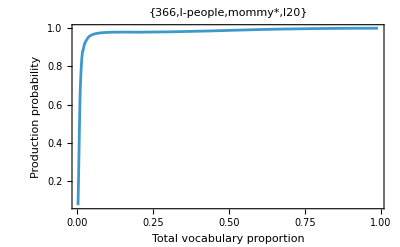

```mathematica
(*例示語について，総語彙割合と産出確率の関係を表示する Show the relationship between total vocabulary proportion and production probability for an example word*)exampleItem=366;
ParametricPlot[{fall@@centerTrajectoryPoint3[t],fitem[exampleItem]@@centerTrajectoryPoint3[t]},{t,1,Length[meanzMF3]},AspectRatio->1/GoldenRatio,PlotLabel->fitem3[exampleItem],Frame->True,FrameLabel->{"Total vocabulary proportion","Production probability"},FrameStyle->14,PlotRange->All]
```

```mathematica
(*各語の25％・50％・75％産出確率点を計算する Compute the 25%,50%,and 75% production-probability thresholds for every word*)
productionProbabilityLevels={0.25,0.50,0.75};
percentilelist=Table[pTot3[item,probability],{item,1,680},{probability,productionProbabilityLevels}];

(*50％産出確率点を各語のVoAとする Use the 50% production-probability threshold as the VoA for each word*)
wordVoA=percentilelist[[All,2]];
```

```mathematica
<|"Dimensions"->Dimensions[percentilelist],"NumericValues"->Count[Flatten[percentilelist],_?NumericQ]|>
```

<|Dimensions→{680,3},NumericValues→2040|>

```mathematica
fitem3[261]
```

{261,i-furniture_rooms,basement,i1}

```mathematica
(*各語のVoAと，75％点から25％点までの発達幅を組み合わせる Combine each word's VoA with its developmental width from the 25% to the 75% production threshold*)voaSpreadData=Transpose[{wordVoA,percentilelist[[All,3]]-percentilelist[[All,1]]}];

<|"Dimensions"->Dimensions[voaSpreadData],"NumericValues"->Count[Flatten[voaSpreadData],_?NumericQ]|>
```

<|Dimensions→{680,2},NumericValues→1360|>

```mathematica
(*各点に語情報のツールチップを付ける Attach word-information tooltips to the points*)voaSpreadWithTooltips=MapThread[Tooltip[#1,#2]&,{voaSpreadData,fitem3/@Range[Length[voaSpreadData]]}];

(*強調表示するカテゴリー Categories to highlight*)
highlightedCategories={5,14};

highlightedVoAData=(voaSpreadWithTooltips[[#[[1]];;#[[2]]]]&)/@catn[[highlightedCategories]];

(*全語を表示する基本図 Base plot containing all words*)
allWordsVoAPlot=ListPlot[voaSpreadWithTooltips,PlotStyle->{Green,PointSize[0.006]},AspectRatio->0.7,Frame->True,FrameStyle->14,FrameLabel->{"VoA (50% production threshold)","75% - 25% threshold width"},ImageSize->500,PlotRange->All];

(*選択したカテゴリーを強調する Highlight the selected categories*)
highlightedCategoriesPlot=ListPlot[highlightedVoAData,PlotStyle->PointSize[0.012],PlotLegends->highlightedCategories];

(*Show[allWordsVoAPlot,highlightedCategoriesPlot]*)
```

#### VoAと発達幅の散布図：語情報のTooltipとカテゴリーの強調 Scatter plot of VoA and developmental width with word tooltips and highlighted categories

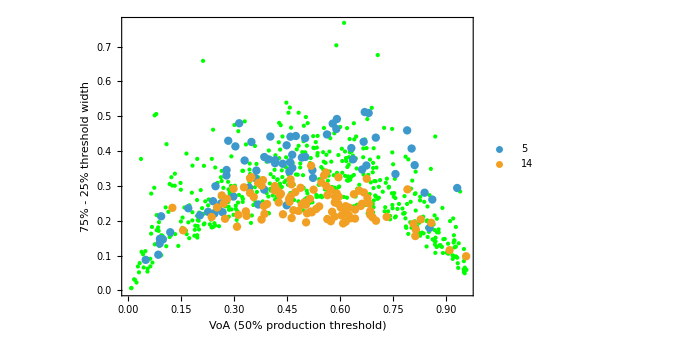

```mathematica
Show[allWordsVoAPlot,highlightedCategoriesPlot]
```

### 22カテゴリー内での語のVoA順序付け Ordering words by VoA within the 22 categories

```mathematica
(*既に計算済みのVoAを各項目に追加し，22カテゴリー内でVoAの小さい順に並べる 
Add the previously computed VoA to each item and sort the items within each of the 22 categories by increasing VoA*)
itemsWithVoA=MapThread[Append,{fitem3/@Range[Length[wordVoA]],wordVoA}];

itemsByCategory=(itemsWithVoA[[#[[1]];;#[[2]]]]&)/@catn;

sortedItemsByCategory=SortBy[#,Last]&/@itemsByCategory;
itemsvoa=Flatten[sortedItemsByCategory,1];

orderbyvoa=itemsvoa[[All,1]];
```

```mathematica
<|"Dimensions"->Dimensions[itemsvoa],"IsPermutation"->Sort[orderbyvoa]===Range[Length[wordVoA]],"CategorySizesMatch"->Length/@sortedItemsByCategory===numitems,"IncreasingWithinCategories"->AllTrue[sortedItemsByCategory,OrderedQ[#[[All,-1]]]&]|>
```

<|Dimensions→{680,5},IsPermutation→True,CategorySizesMatch→True,IncreasingWithinCategories→True|>

#### 総語彙割合ptotからカテゴリー別VoA順語彙の位置への変換 Mapping total vocabulary proportion (ptot) to word-rank position in the category-wise VoA ordering

```mathematica
(*1カテゴリーについて，総語彙割合ptotと語順位置の対応データを作る Construct the mapping data between total vocabulary proportion ptot and word-rank position for one category*)ptotToRankDataForCategory[{firstItem_Integer,lastItem_Integer}]:=Join[{{0,firstItem-1}},Transpose[{itemsvoa[[firstItem;;lastItem,-1]],Range[firstItem,lastItem]}],{{1,lastItem+1}}];

(*22カテゴリーの対応データと線形補間関数を作る Construct the mapping data and linear interpolation functions for the 22 categories*)
ptotToRankData=ptotToRankDataForCategory/@catn;
ptotToRankFunctions=Interpolation[#,InterpolationOrder->1]&/@ptotToRankData;

Clear[ptotToRank];
ptotToRank[nc_Integer]:=ptotToRankFunctions[[nc]];
```

```mathematica
<|"NumberOfCategories"->Length[ptotToRankData],"AllDataNumeric"->AllTrue[ptotToRankData,MatrixQ[#,NumericQ]&],"EndpointRowsMatch"->And@@MapThread[(First[#1]==={0,#2[[1]]-1}&&Last[#1]==={1,#2[[2]]+1})&,{ptotToRankData,catn}],"NumberOfFunctions"->Length[ptotToRankFunctions]|>
```

<|NumberOfCategories→22,AllDataNumeric→True,EndpointRowsMatch→True,NumberOfFunctions→22|>

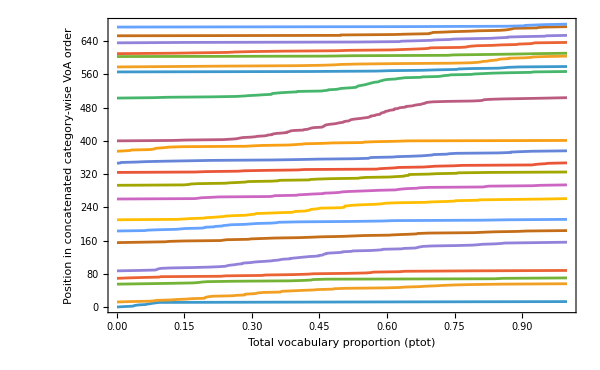

```mathematica
(*22カテゴリーそれぞれについて，ptotに対応するVoA順の語順位置を描く．この位置は leftRightDifferencePlotAt と outInDifferencePlotAt で 縦破線の横軸座標に用いる．ptot=0，1 は補間用の端点である．
Plot the ptot-to-position mapping for each of the 22 categories in the concatenated,category-wise VoA order.These positions set the x coordinates of the dashed vertical lines in leftRightDifferencePlotAt and outInDifferencePlotAt.The points at ptot=0 and 1 are interpolation anchors.*)Module[{p},Plot[Evaluate[Table[ptotToRank[nc][p],{nc,1,Length[catn]}]],{p,0,1},Frame->True,FrameLabel->{"Total vocabulary proportion (ptot)","Position in concatenated category-wise VoA order"},PlotRange->All,ImageSize->600,FrameStyle->13]]
```

#### 潜在空間の中央発達軌道と総語彙割合0.5の等値面上の５点 Center developmental trajectory and five points on the ptot = 0.5 isosurface

```mathematica
(*CDIデータ，全0・全1プロファイル，中央発達軌道を表示する．Show the CDI data，the all-zero and all-one profiles，and the center developmental trajectory．*)pdevtmp=Show[latentSpaceReferencePlot,ParametricPlot3D[Evaluate@Through[devcenter3f[t]],{t,1,Length[meanzMF3]},PlotStyle->Green]];
```

```mathematica
(*ptot=0.5 の等総語彙割合面上に，5つの発達軌道位置を表示する．Show the five developmental-trajectory positions on the equal-vocabulary-proportion surface at ptot=0.5．*)examplePtot=0.5;
examplePtotSurface=ListContourPlot3D[gridall,Contours->{examplePtot},ContourStyle->Directive[cl[[2]],Opacity[0.2]],PlotRange->{{-4,4},{-4,4},{-4,4}}];
exampleTrajectoryPoints=<|"Center"->zcenter3[examplePtot],"Left"->zleft3[examplePtot],"Right"->zright3[examplePtot],"In"->zin3[examplePtot],"Out"->zout3[examplePtot]|>;
exampleTrajectoryColors=<|"Center"->Green,"Left"->Magenta,"Right"->Cyan,"In"->Cyan,"Out"->Magenta|>;

exampleTrajectoryGraphic=Graphics3D[KeyValueMap[{exampleTrajectoryColors[#1],PointSize[0.02],Point[#2]}&,exampleTrajectoryPoints]];

trajectoryOverviewPlot=Show[pdevtmp,examplePtotSurface,exampleTrajectoryGraphic]
```

-Graphics3D-

#### 中央軌道上の総語彙割合0.5における語ごとの表出確率 Word-wise production probabilities on the center trajectory at ptot = 0.5 center (green) ptot = 0.5

以下の図では，22カテゴリーを順に連結し，各カテゴリー内の語を VoA の小さい順に並べる．ここでの VoA は，中央発達軌道上で語の予測表出確率が0.5に達する総語彙割合であり，値が小さいほど早い獲得段階に対応する．  

In the plots below, the 22 categories are concatenated, and words within each category are ordered by increasing VoA. Here VoA is the total vocabulary proportion at which a word’s predicted production probability reaches 0.5 along the center developmental trajectory; smaller values correspond to earlier acquisition stages.

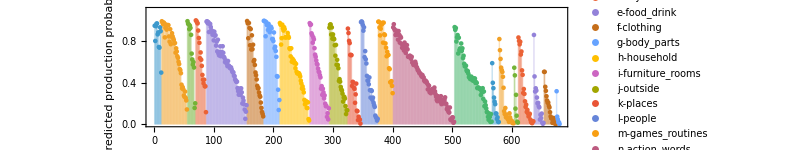

```mathematica
(*カテゴリー内でVoA順に並べた各語の推定表出確率．
Predicted production probabilities ordered by VoA within each category.*)
plotPtot=0.5;
orderedProbabilities=predict[zcenter3[plotPtot]][[orderbyvoa]];

orderedPoints=MapThread[Tooltip[{#1,#2},fitem3[#3]]&,{Range[Length[orderedProbabilities]],orderedProbabilities,orderbyvoa}];

centerWordProbabilityPlot=ListPlot[(orderedPoints[[#[[1]];;#[[2]]]]&/@catn),Filling->Axis,Frame->True,FrameLabel->{"Word rank (VoA order within category)","Predicted production probability"},ImageSize->600,AspectRatio->1/4,PlotRange->{0,1.1},PlotLegends->Placed[catname,Right]];

centerWordProbabilityPlot
```

#### 総語彙割合0.5における Left・Right・Out・In の語ごとの表出確率 Word-wise production probabilities at Left, Right, Out, and In for ptot = 0.5

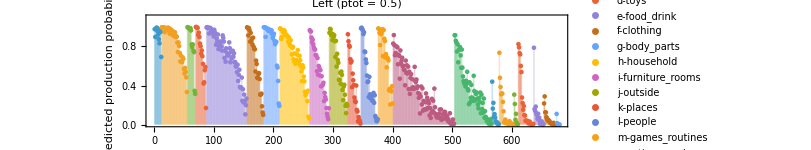
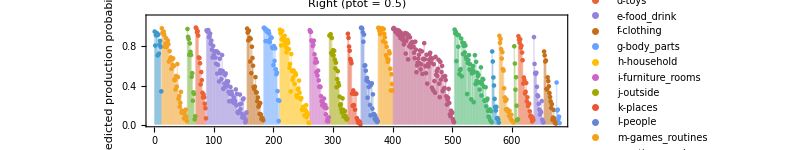
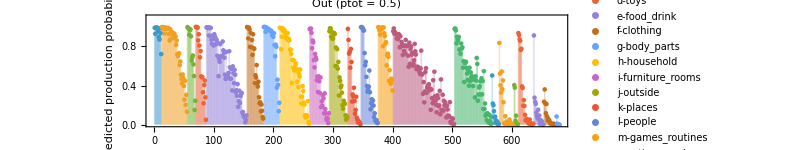
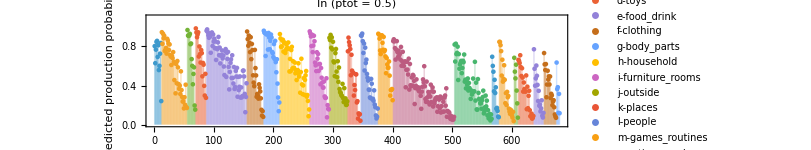

```mathematica
wordProbabilityPlot[trajectory_,name_]:=Module[{probabilities,points},probabilities=predict[trajectory[plotPtot]][[orderbyvoa]];
points=MapThread[Tooltip[{#1,#2},fitem3[#3]]&,{Range[Length[probabilities]],probabilities,orderbyvoa}];
ListPlot[(points[[#[[1]];;#[[2]]]]&/@catn),Filling->Axis,Frame->True,FrameLabel->{"Word rank (VoA order within category)","Predicted production probability"},PlotRange->{0,1.1},AspectRatio->1/4,ImageSize->600,PlotLegends->Placed[catname,Right],PlotLabel->Row[{name," (ptot = ",plotPtot,")"}]]];

leftWordProbabilityPlot=wordProbabilityPlot[zleft3,"Left"];
rightWordProbabilityPlot=wordProbabilityPlot[zright3,"Right"];
outWordProbabilityPlot=wordProbabilityPlot[zout3,"Out"];
inWordProbabilityPlot=wordProbabilityPlot[zin3,"In"];

Column[{leftWordProbabilityPlot,rightWordProbabilityPlot,outWordProbabilityPlot,inWordProbabilityPlot},Spacings->2]
```

#### 異なる総語彙割合における Left–Right 軸（nominality）の語ごとの表出確率差 Word-wise production-probability differences along the Left–Right (nominality) axis at different total vocabulary proportions

各カテゴリーの破線は，VoA 順に並んだ語のうち，VoA が図の ptot と等しくなる語順位置を補間して示す．破線の左側には VoA が ptot より小さい語，右側には大きい語が並ぶ．

In each category, the dashed line marks the interpolated word position where VoA equals the plotted ptot . Words to its left have smaller VoA, and words to its right have larger VoA .

```mathematica
(*任意の総語彙割合で Left－Right の語ごとの表出確率差を描く．Plot word-wise Left－Right production-probability differences at a specified total vocabulary proportion.*)Clear[leftRightDifferencePlotAt];

leftRightDifferencePlotAt[ptot_?NumericQ]:=Module[{values,points,yRange={-0.9,0.9}},values=(predict[zleft3[ptot]]-predict[zright3[ptot]])[[orderbyvoa]];
points=MapThread[Tooltip[{#1,#2},fitem3[#3]]&,{Range[Length[values]],values,orderbyvoa}];
ListPlot[(points[[#[[1]];;#[[2]]]]&/@catn),Filling->Axis,Frame->True,FrameLabel->{"Word position (categories concatenated; VoA order within each)","Production probability (Left - Right)"},ImageSize->600,AspectRatio->1/2,PlotRange->yRange,PlotLegends->Placed[catname,Right],PlotLabel->Row[{"ptot = ",ptot}],Epilog->Table[{Dashed,Thin,Line[{{ptotToRank[nc][ptot],yRange[[1]]},{ptotToRank[nc][ptot],yRange[[2]]}}]},{nc,Length[catn]}]]];

(* leftRightDifferencePlotAt[0.5]*)
```

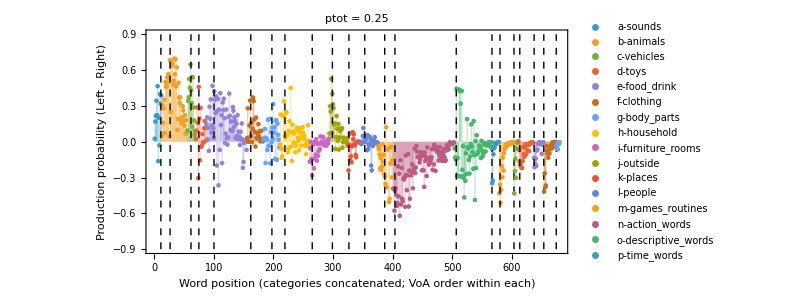

```mathematica
leftRightDifferencePlotAt[0.25]
```

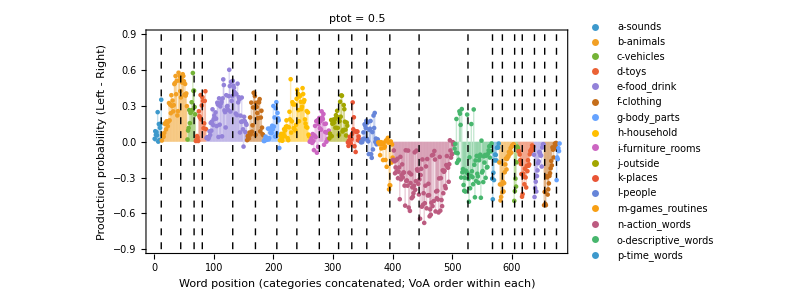

```mathematica
leftRightDifferencePlotAt[0.5]
```

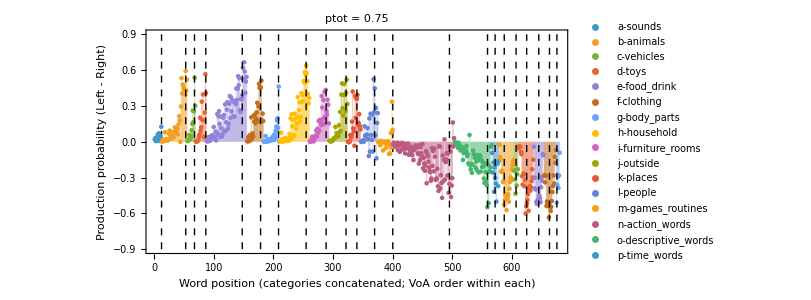

```mathematica
leftRightDifferencePlotAt[0.75]
```

```mathematica
listLR=Table[leftRightDifferencePlotAt[ptot],{ptot,0.1,0.9,0.1}];
```

```mathematica
ListAnimate[listLR]
```

```mathematica
(*
videoPath=FileNameJoin[{NotebookDirectory[],"Eingish_LeftRight_nominality_ptot_0p1_to_0p9.mp4"}];
Export[videoPath,listLR,"MP4",FrameRate->1]
*)
```

#### 異なる総語彙割合における Out–In 軸（commonality）の語ごとの表出確率差 Word-wise production-probability differences along the Out–In (commonality) axis at different total vocabulary proportions

各カテゴリーの破線は，VoA 順に並んだ語のうち，VoA が図の ptot と等しくなる語順位置を補間して示す．破線の左側には VoA が ptot より小さい語，右側には大きい語が並ぶ．

In each category, the dashed line marks the interpolated word position where VoA equals the plotted ptot. Words to its left have smaller VoA, and words to its right have larger VoA.

```mathematica
(*任意の総語彙割合で Out－In 軸（commonality）の 語ごとの表出確率差を描く．Plot word-wise Out－In production-probability differences at a specified total vocabulary proportion.*)Clear[outInDifferencePlotAt];

outInDifferencePlotAt[ptot_?NumericQ]:=Module[{values,points,yRange={-0.8,0.8}},values=(predict[zout3[ptot]]-predict[zin3[ptot]])[[orderbyvoa]];
points=MapThread[Tooltip[{#1,#2},#3]&,{Range[Length[values]],values,itemsvoa}];
ListPlot[(points[[#[[1]];;#[[2]]]]&/@catn),Filling->Axis,Frame->True,FrameLabel->{"Word position (categories concatenated; VoA order within each)","Production probability (Out - In)"},ImageSize->600,AspectRatio->1/2,PlotRange->yRange,PlotLegends->Placed[catname,Right],PlotLabel->Row[{"ptot = ",ptot}],Epilog->Table[{Dashed,Thin,Line[{{ptotToRank[nc][ptot],yRange[[1]]},{ptotToRank[nc][ptot],yRange[[2]]}}]},{nc,Length[catn]}]]];
```

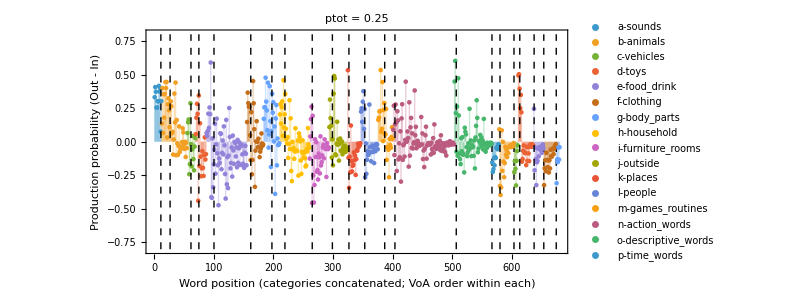

```mathematica
outInDifferencePlotAt[0.25]
```

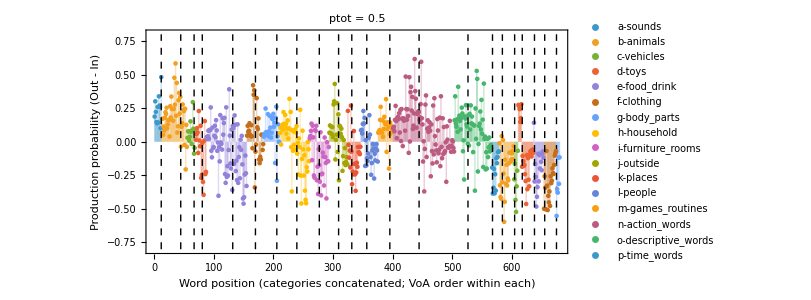

```mathematica
outInDifferencePlotAt[0.5]
```

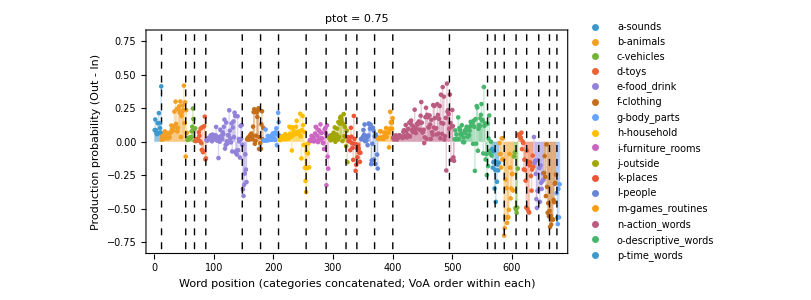

```mathematica
outInDifferencePlotAt[0.75]
```

```mathematica
listOI=Table[outInDifferencePlotAt[ptot],{ptot,0.1,0.9,0.1}];
```

```mathematica
ListAnimate[listOI]
```

```mathematica
(*
videoPath=FileNameJoin[{NotebookDirectory[],"English_OutIn_commonality_ptot_0p1_to_0p9.mp4"}];
Export[videoPath,listOI,"MP4",FrameRate->1]
*)
```

```mathematica
(*同じ総語彙割合における Out と In の表出確率の対数比を描く．Plot the log production-probability ratio of Out to In at the same total vocabulary proportion.*)
(*
logRatioPtot=0.5;

outProbabilities=predict[zout3[logRatioPtot]][[orderbyvoa]];
inProbabilities=predict[zin3[logRatioPtot]][[orderbyvoa]];
outInLogRatios=Log[outProbabilities/inProbabilities];
logRatioYRange=MinMax[outInLogRatios];

outInLogRatioPoints=MapThread[Tooltip[{#1,#2},#3]&,{Range[Length[outInLogRatios]],outInLogRatios,itemsvoa}];

outInLogRatioPlot=ListPlot[(outInLogRatioPoints[[#[[1]];;#[[2]]]]&/@catn),Filling->Axis,Frame->True,FrameLabel->{"Word position (categories concatenated; VoA order within each)","Log production-probability ratio (Out / In)"},ImageSize->600,AspectRatio->1/2,PlotRange->All,PlotLegends->Placed[catname,Right],PlotLabel->Row[{"ptot = ",logRatioPtot}],Epilog->Table[{Dashed,Thin,Line[{{ptotToRank[nc][logRatioPtot],logRatioYRange[[1]]},{ptotToRank[nc][logRatioPtot],logRatioYRange[[2]]}}]},{nc,Length[catn]}]];

outInLogRatioPlot*)
```

#### 等総語彙割合面上の5つの発達軌道位置 Five developmental-trajectory positions on an equal-vocabulary-proportion surface

```mathematica
(*CDIデータ，全0・全1プロファイル，中央発達軌道を表示する．Show the CDI data，the all-zero and all-one profiles，and the center developmental trajectory．*)pdevtmp=Show[latentSpaceReferencePlot,ParametricPlot3D[Evaluate@Through[devcenter3f[t]],{t,1,Length[meanzMF3]},PlotStyle->Green]];
```

```mathematica
(*ptot=0.5 の等総語彙割合面上に，5つの発達軌道位置を表示する．Show the five developmental-trajectory positions on the equal-vocabulary-proportion surface at ptot=0.5．*)examplePtot=0.5;
examplePtotSurface=ListContourPlot3D[gridall,Contours->{examplePtot},ContourStyle->Directive[cl[[2]],Opacity[0.2]],PlotRange->{{-4,4},{-4,4},{-4,4}}];
exampleTrajectoryPoints=<|"Center"->zcenter3[examplePtot],"Left"->zleft3[examplePtot],"Right"->zright3[examplePtot],"In"->zin3[examplePtot],"Out"->zout3[examplePtot]|>;
exampleTrajectoryColors=<|"Center"->Green,"Left"->Magenta,"Right"->Cyan,"In"->Cyan,"Out"->Magenta|>;

exampleTrajectoryGraphic=Graphics3D[KeyValueMap[{exampleTrajectoryColors[#1],PointSize[0.02],Point[#2]}&,exampleTrajectoryPoints]];

trajectoryOverviewPlot=Show[pdevtmp,examplePtotSurface,exampleTrajectoryGraphic]
```

-Graphics3D-

### 軌道周辺の局所事後標準偏差と潜在点生成 Local posterior standard deviations and latent-point generation around trajectories

```mathematica
(*潜在点zに最も近い3つの観測CDIプロファイルを選び，Encoderの事後標準偏差を潜在次元ごとに平均する．ここで平均するのは分散ではなく標準偏差である．
The three observed CDI profiles nearest to latent point z are selected，and their encoder posterior standard deviations are averaged separately for each latent dimension．The averaged quantities are standard deviations，not variances．*)
nNearestProfiles=3;
nearestProfileIndices[z_]:=TakeSmallestBy[Range[Length[zdataEsort]],Norm[z-zdataEsort[[#]]]&,nNearestProfiles];

z2σ[z_]:=Module[{nearestIndices,nearestProfiles},nearestIndices=nearestProfileIndices[z];
nearestProfiles=alldatasort[[nearestIndices+1,5;;]];
Mean[Exp[0.5*tologsigma[#]]&/@nearestProfiles]];
```

```mathematica
(*軌道上の点zcを平均とし，局所的に推定した事後標準偏差から 対角共分散行列を作り，num個の潜在点を再現可能な形で生成する．Generate num reproducible latent-space points around trajectory point zc，using a diagonal covariance matrix constructed from the locally estimated posterior standard deviations．

nNearestProfilesは局所標準偏差の推定に使う近傍プロファイル数であり，numは生成する潜在点の数である．nNearestProfiles is the number of neighboring profiles used to estimate local standard deviations，whereas num is the number of generated points．*)

generate[zc_,num_Integer,seed_Integer]:=BlockRandom[SeedRandom[seed,Method->"MersenneTwister"];
RandomVariate[MultinormalDistribution[zc,DiagonalMatrix[z2σ[zc]^2]],num]];
```

```mathematica
(*引き戻し前の生成サンプルと目標の等総語彙割合面を比較する．Compare the generated samples before projection with the target equal-total-vocabulary-proportion surface.*)ptot=0.5;
zwork=zout3[ptot];

(*zworkの周囲に，引き戻し前のサンプルを生成する．Generate samples around zwork before projection.*)
rawSamples=generate[zwork,100,9999];

(*zworkと局所標準偏差を表示する．Show zwork and its local standard deviations.*)
localUncertaintyPlot=ListPointPlot3D[{MapThread[Around,{zwork,z2σ[zwork]}]},PlotStyle->Directive[Blue,PointSize[0.01],Thickness[0.003]]];

(*引き戻し前の生成サンプルを表示する．Show the generated samples before projection.*)
rawSamplePlot=ListPointPlot3D[rawSamples,PlotStyle->Directive[Blue,PointSize[0.008]]];

(*目標とする等総語彙割合面を表示する．Show the target equal-total-vocabulary-proportion surface.*)
targetPtotSurface=ListContourPlot3D[gridall,Contours->{ptot},ContourStyle->Directive[cl[[2]],Opacity[0.2]]];

(*同じ総語彙割合に対応する5本の軌道上の位置を表示する．Show the positions on the five trajectories at the same total vocabulary proportion.*)
trajectoryPointsAtPtot=<|"Center"->zcenter3[ptot],"Left"->zleft3[ptot],"Right"->zright3[ptot],"In"->zin3[ptot],"Out"->zout3[ptot]|>;

trajectoryColors=<|"Center"->Green,"Left"->Magenta,"Right"->Cyan,"In"->Cyan,"Out"->Magenta|>;

trajectoryPointGraphic=Graphics3D[KeyValueMap[{trajectoryColors[#1],PointSize[0.02],Point[#2]}&,trajectoryPointsAtPtot]];

rawSampleDeviationPlot=Show[localUncertaintyPlot,rawSamplePlot,targetPtotSurface,Graphics3D[{{Black,PointSize[0.03],Point[zAllZero]},{Red,PointSize[0.03],Point[zAllOne]}}],trajectoryPointGraphic,BoxRatios->1,PlotRange->{{-4,4},{-4,4},{-4,4}},AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},ViewPoint->{1.0,-3,1},ImageSize->400]
```

-Graphics3D-

#### 引き戻し前の生成サンプルの等総語彙割合面からのずれ Deviation of generated samples from the equal-total-vocabulary-proportion surface before projection

```mathematica
(*各軌道位置の周囲に生成した，引き戻し前のサンプルについて総語彙数の統計量を計算する．Calculate total-vocabulary statistics for samples generated around each trajectory position before projection.*)ClearAll[rawSampleVocabularyStats];
Options[rawSampleVocabularyStats]={"Ptot"->0.5,"NSamples"->100,"Seed"->9999};

rawSampleVocabularyStats[trajectoryFunction_,OptionsPattern[]]:=Module[{ptot=OptionValue["Ptot"],nSamples=OptionValue["NSamples"],seed=OptionValue["Seed"],latentCenter,generatedSamples,vocabularyTotals,targetVocabulary,meanVocabulary,absoluteDeviations},latentCenter=trajectoryFunction[ptot];
generatedSamples=generate[latentCenter,nSamples,seed];
vocabularyTotals=Total/@(predict/@generatedSamples);
targetVocabulary=Total[predict[latentCenter]];
meanVocabulary=Mean[vocabularyTotals];
absoluteDeviations=Abs[vocabularyTotals-targetVocabulary];
<|"CenterVocabulary"->targetVocabulary,"Mean"->meanVocabulary,"SD"->StandardDeviation[vocabularyTotals],"Max"->Max[vocabularyTotals],"Min"->Min[vocabularyTotals],"MaxMinusMean"->Max[vocabularyTotals]-meanVocabulary,"MinMinusMean"->Min[vocabularyTotals]-meanVocabulary,"MaxRelativeDeviation"->(Max[vocabularyTotals]-meanVocabulary)/meanVocabulary,"MinRelativeDeviation"->(Min[vocabularyTotals]-meanVocabulary)/meanVocabulary,"MeanAbsoluteDeviationFromTarget"->Mean[absoluteDeviations],"SDAbsoluteDeviationFromTarget"->StandardDeviation[absoluteDeviations]|>]
```

```mathematica
(*5本の軌道関数を名前と対応づけ，引き戻し前の生成サンプルについて 軌道ごとの総語彙数統計量を計算する．Associate the five trajectory functions with their names and calculate total-vocabulary statistics for the generated samples before projection.*)trajectoryFunctionsForDeviation=<|"Center"->zcenter3,"Left"->zleft3,"Right"->zright3,"In"->zin3,"Out"->zout3|>;

rawSampleStatsByTrajectory=Map[rawSampleVocabularyStats[#,"Ptot"->0.5,"NSamples"->100,"Seed"->9999]&,trajectoryFunctionsForDeviation];
```

```mathematica
(*5本の軌道について，引き戻し前の生成サンプルの総語彙数を比較する．Compare total vocabulary sizes of the generated samples before projection across the five trajectories.*)rawSampleDeviationRows=KeyValueMap[Function[{position,statistics},{position,statistics["CenterVocabulary"],statistics["Mean"],statistics["SD"],statistics["Max"],statistics["Min"],statistics["MaxMinusMean"],statistics["MinMinusMean"],100 statistics["MaxRelativeDeviation"],100 statistics["MinRelativeDeviation"],statistics["MeanAbsoluteDeviationFromTarget"],statistics["SDAbsoluteDeviationFromTarget"]}],rawSampleStatsByTrajectory];

rawSampleDeviationTable=Grid[Prepend[rawSampleDeviationRows,{"Position","Target","Mean","SD","Max","Min","Max−Mean","Min−Mean","Max−Mean (%)","Min−Mean (%)","Mean |Sample−Target|","SD |Sample−Target|"}],Frame->All]
```

Position | Target | Mean | SD | Max | Min | Max−Mean | Min−Mean | Max−Mean (%) | Min−Mean (%) | Mean |Sample−Target| | SD |Sample−Target|
Center | 340.054 | 341.286 | 9.20591 | 366.888 | 321.452 | 25.6014 | -19.834 | 7.50146 | -5.81154 | 7.12455 | 5.91688
Left | 339.999 | 340.937 | 7.66871 | 360.875 | 321.844 | 19.9379 | -19.0933 | 5.84798 | -5.60025 | 5.97235 | 4.86495
Right | 340.014 | 340.85 | 7.59498 | 361.833 | 322.914 | 20.9832 | -17.9361 | 6.15614 | -5.26217 | 5.85632 | 4.87309
In | 340.039 | 340.544 | 13.2431 | 366.79 | 298.51 | 26.2461 | -42.0337 | 7.70712 | -12.3431 | 10.6556 | 7.80686
Out | 339.998 | 341.136 | 7.53917 | 362.293 | 324.569 | 21.1563 | -16.5677 | 6.20172 | -4.85662 | 5.87136 | 4.82992

#### 生成点を指定した等総語彙割合面へ移動する Moving generated points onto a specified equal-total-vocabulary-proportion surface

```mathematica
(*出発点における総語彙割合の勾配方向に沿う直線上を移動し，指定した等総語彙割合面との交点を求める．Move along the line defined by the gradient of total vocabulary proportion at the starting point and find its intersection with the specified equal-total-vocabulary-proportion surface.*)
```

```mathematica
movedPt[startpt_,ptot_]:= Module[{vec,x,y,z,init,normalv,vec1,ptot1,ans,ansvec},
vec={x,y,z};
init=Rule@@@Transpose[{vec,startpt}];
normalv=Normalize[Grad[fall[x,y,z],{x,y,z}]/.init];
vec1[t_]:= startpt + normalv t;
ptot1[t_] := Flatten[fall[#[[1]],#[[2]],#[[3]]]&/@{vec1[t]}][[1]];
    ans=FindRoot[ptot1[t]==ptot,{t,0.}];
ansvec = vec1[t]/.ans
]
```

#### 指定した等総語彙割合面上での潜在サンプル生成 Generating latent samples on a specified equal-total-vocabulary-proportion surface

```mathematica
(*zcは，目標とする総語彙割合ptotに対応する軌道上の点とする．zcの周囲に生成したnum個の潜在点を，同じptotの等総語彙割合面へ移動する．Let zc be a trajectory point corresponding to the target total vocabulary proportion ptot.The function generates num latent points around zc and moves them onto the equal-total-vocabulary-proportion surface at the same ptot.*)
```

```mathematica
createZdata[zc_,ptot_,num_,seed_]:=
Module[{sample},sample=generate[zc,num,seed];
movedPt[#,ptot]&/@sample]
```

#### 引き戻し後の潜在サンプルと等総語彙割合面 Projected latent samples on the equal-total-vocabulary-proportion surface

```mathematica
(*中心軌道上の点の周囲に生成し，指定した等総語彙割合面へ移動した 潜在サンプルを表示する．Show latent samples generated around a point on the center trajectory and moved onto the specified equal-total-vocabulary-proportion surface.*)
projectedExamplePtot=0.5;
projectedExampleCenter=zcenter3[projectedExamplePtot];

projectedExampleSamples=createZdata[projectedExampleCenter,projectedExamplePtot,100,1];

projectedUncertaintyPlot=ListPointPlot3D[{MapThread[Around,{projectedExampleCenter,z2σ[projectedExampleCenter]}]},PlotStyle->Directive[Blue,PointSize[0.01],Thickness[0.003]]];

projectedSamplePlot=ListPointPlot3D[projectedExampleSamples,PlotStyle->Directive[Blue,PointSize[0.008]]];

projectedTargetSurface=ListContourPlot3D[gridall,Contours->{projectedExamplePtot},ContourStyle->Directive[cl[[2]],Opacity[0.2]]];

projectedTrajectoryPoints=<|"Center"->zcenter3[projectedExamplePtot],"Left"->zleft3[projectedExamplePtot],"Right"->zright3[projectedExamplePtot],"In"->zin3[projectedExamplePtot],"Out"->zout3[projectedExamplePtot]|>;

projectedTrajectoryColors=<|"Center"->Green,"Left"->Magenta,"Right"->Cyan,"In"->Cyan,"Out"->Magenta|>;

projectedTrajectoryGraphic=Graphics3D[KeyValueMap[{projectedTrajectoryColors[#1],PointSize[0.02],Point[#2]}&,projectedTrajectoryPoints]];

projectedSampleSurfacePlot=Show[projectedUncertaintyPlot,projectedSamplePlot,projectedTargetSurface,Graphics3D[{{Black,PointSize[0.03],Point[zAllZero]},{Red,PointSize[0.03],Point[zAllOne]}}],projectedTrajectoryGraphic,BoxRatios->1,PlotRange->{{-4,4},{-4,4},{-4,4}},AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},ViewPoint->{1.0,-3,1}]
```

-Graphics3D-

#### 5本の発達軌道に沿った合成CDIプロファイルの生成 Generation of synthetic CDI profiles along the five developmental trajectories

```mathematica
(*軌道とptot水準ごとに再現可能な乱数seedを定める．
Define reproducible random seeds for each trajectory and ptot level.*)
seedIn[k_]:=Hash[{"in",k},"SHA256"]
seedOut[k_]:=Hash[{"out",k},"SHA256"]
seedLeft[k_]:=Hash[{"Left",k},"SHA256"]
seedRight[k_]:=Hash[{"right",k},"SHA256"]
seedCenter[k_]:=Hash[{"center",k},"SHA256"]
```

```mathematica
(*1本の軌道について，ptot=0.1から0.9まで，各水準で総語彙割合一定面上の潜在点を生成し，decoderで合成CDIプロファイルへ変換する．For one trajectory,generate latent points on the corresponding constant-total-vocabulary-proportion surface at each ptot level from 0.1 to 0.9 and decode them into synthetic CDI profiles.*)
ClearAll[generateTrajectoryCDIRows];

generateTrajectoryCDIRows[trajectoryFunction_,seedFunction_,numSamples_Integer:100]:=Flatten[Table[Module[{ptot=k/10.,latentSamples,cdiSamples},latentSamples=createZdata[trajectoryFunction[ptot],ptot,numSamples,seedFunction[k]];
cdiSamples=predict/@latentSamples;
Transpose[Join[{ConstantArray[ptot,numSamples]},Transpose[latentSamples],Transpose[cdiSamples]]]],{k,1,9}],1]
```

```mathematica
(*各軌道関数と対応するseed関数をまとめる．Associate each trajectory function with its corresponding seed function.*)trajectoryGenerationSpecifications=<|"Center"->{zcenter3,seedCenter},"Left"->{zleft3,seedLeft},"Right"->{zright3,seedRight},"In"->{zin3,seedIn},"Out"->{zout3,seedOut}|>;
```

```mathematica
(*5本の軌道について，各ptot水準で100個の潜在点を生成し，decoder出力と列名をまとめる．
For each of the five trajectories,generate 100 latent points at each ptot level and combine them with the decoder outputs and column names.*)
syntheticCDIRowsByTrajectory=Map[generateTrajectoryCDIRows[#[[1]],#[[2]],100]&,trajectoryGenerationSpecifications];

syntheticCDIColumns=Join[{"pTot","Zx","Zy","Zz"},alldata[[1,5;;]]];
syntheticCDIDataByTrajectory=Map[Prepend[#,syntheticCDIColumns]&,syntheticCDIRowsByTrajectory];
```

```mathematica
(*軌道ごとのデータを後続解析用の個別変数に取り出す．Extract the trajectory-specific datasets into individual variables for subsequent analyses.*)
ZCDIcenter=syntheticCDIDataByTrajectory["Center"];
ZCDIleft=syntheticCDIDataByTrajectory["Left"];
ZCDIright=syntheticCDIDataByTrajectory["Right"];
ZCDIin=syntheticCDIDataByTrajectory["In"];
ZCDIout=syntheticCDIDataByTrajectory["Out"];
```

```mathematica
(* Export data *)
```

```mathematica
(* Export["ZCDIout.csv",ZCDIout];
Export["ZCDIin.csv",ZCDIin];
Export["ZCDIleft.csv",ZCDIleft];
Export["ZCDIright.csv",ZCDIright];
Export["ZCDIcenter.csv",ZCDIcenter];*)
```

#### システマティックに生成した潜在サンプルの確認 Verification of systematically generated latent samples

```mathematica
(*In軌道のptot=0.4を代表例とし，システマティックに生成された潜在点が対応する等総語彙割合面上にあることを確認する．Using the In trajectory at ptot=0.4 as a representative example,verify that the systematically generated latent samples lie on the corresponding equal-total-vocabulary-proportion surface.*)
representativeSyntheticTrajectory="In";
representativeSyntheticPtot=0.4;

representativeSyntheticRows=Select[Rest[syntheticCDIDataByTrajectory[representativeSyntheticTrajectory]],Abs[#[[1]]-representativeSyntheticPtot]<10^-12&];
representativeSyntheticCoordinates=representativeSyntheticRows[[All,2;;4]];
representativeSyntheticCenter=trajectoryGenerationSpecifications[representativeSyntheticTrajectory][[1]][representativeSyntheticPtot];
representativeSyntheticSamplePlot=ListPointPlot3D[representativeSyntheticCoordinates,PlotStyle->Directive[Blue,PointSize[0.008]]];
representativeSyntheticSurface=ListContourPlot3D[gridall,Contours->{representativeSyntheticPtot},ContourStyle->Directive[cl[[2]],Opacity[0.2]]];

systematicGenerationCheckPlot=Show[representativeSyntheticSamplePlot,representativeSyntheticSurface,Graphics3D[{Darker[Green],PointSize[0.03],Point[representativeSyntheticCenter]}],BoxRatios->1,PlotRange->{{-4,4},{-4,4},{-4,4}},AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},ViewPoint->{1.0,-3,1}]
```

-Graphics3D-

#### 4名の縦断的語彙発達の潜在空間への投影 Projection of longitudinal vocabulary development for four children into the latent space

```mathematica
(*Roy et al.（2015）の各語の初出月齢aoa_Mから，10～25か月の累積二値CDI-like profilesを作成し，VAE潜在空間へ投影する．Construct cumulative binary CDI-like profiles from 10 to 25 months using each word's first-production age (aoa_M) from Roy et al.(2015),and project them into the VAE latent space.*)(*Roy child:age of first production for the 680 CDI items*)
debRoyAoAM=debRoy3D[[3;;,9]];
debRoyAgeM=Range[10,25];
(*Cumulative binary vocabulary profiles at 10–25 months*)
debRoyProfiles=Table[If[NumericQ[#]&&#<=ageM,1,0]&/@debRoyAoAM,{ageM,debRoyAgeM}];

(*Projection into the three-dimensional latent space*)
debRoyMonth=toz/@debRoyProfiles;
```

```mathematica
royCDIProfile[ageM_?NumericQ]:=If[NumericQ[#]&&#<=ageM,1,0]&/@debRoyAoAM
```

```mathematica
<|"Items with AoA"->Count[debRoyAoAM,_?NumericQ],
"Binary profile dimensions"->Dimensions[debRoyProfiles],"Values in binary profiles"->Sort@DeleteDuplicates@Flatten[debRoyProfiles],"Latent-coordinate dimensions"->Dimensions[debRoyMonth]|>
```

<|Items with AoA→364,Binary profile dimensions→{16,680},Values in binary profiles→{0,1},Latent-coordinate dimensions→{16,3}|>

```mathematica
baseplot1=Show[
ListPointPlot3D[zdataE,BoxRatios->1,PlotRange->{{-4,4},{-4,4},{-4,4}},PlotStyle->PointSize[0.0035],AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},ViewPoint->{1.0,-3,1}],
Graphics3D[{PointSize[0.03],Point[toz[Table[0,d]]]}],
Graphics3D[{Red,PointSize[0.03],Point[toz[Table[1,d]]]}]
];
```

```mathematica
(*SAYCamの3名について，各時点のCDI profileをVAE潜在空間へ投影する．Project the CDI profile at each time point for the three SAYCam children into the VAE latent space.*)ClearAll[sayCamLatentTrajectory];

sayCamLatentTrajectory[childName_String]:=toz/@Select[dataSAY,#[[3]]===childName&][[All,7;;]];

sayCamChildNames={"Sam","Alice","Asa"};

sayCamLatentTrajectories=AssociationThread[sayCamChildNames,sayCamLatentTrajectory/@sayCamChildNames];
samZ=sayCamLatentTrajectories["Sam"];
aliceZ=sayCamLatentTrajectories["Alice"];
asaZ=sayCamLatentTrajectories["Asa"];

Dimensions/@sayCamLatentTrajectories
```

<|Sam→{15,3},Alice→{12,3},Asa→{6,3}|>

```mathematica
longitudinalTrajectoryPlot=Show[baseplot1,
ListPointPlot3D[meanfiltervecandend[meanzdataE,nfilter,6],AspectRatio->1,PlotStyle->{{Green,PointSize[0.012]}}],
(*ListPointPlot3D[MovingAverage[typicalmean,3],PlotStyle->{{Blue,PointSize[0.014]}},PlotLegends->{"typical"}],
ListPointPlot3D[MovingAverage[latemean,3],PlotStyle->{{Cyan,PointSize[0.014]}},PlotLegends->{"late"}],*)
ListLinePlot3D[{samZ,aliceZ,debRoyMonth[[1;;-1]],asaZ},PlotMarkers->Automatic,PlotStyle->{{Orange,Thickness[0.003]},{Black,Thickness[0.003]},{Magenta,Thickness[0.003]},{Cyan,Thickness[0.003]}},PlotLegends->{"Sam","Alice","Roy","Asa"}]
]
```

-Graphics3D-

```mathematica
(*Export["FourChildren-Latent3D.cdf",longitudinalTrajectoryPlot];*)
```

#### 潜在空間における局所1 SD軸（Left–Right，In–Out）の定義と可視化 Definition and visualization of local one-SD axes (Left–Right and In–Out) in the latent space

```mathematica
(*指定された総語彙割合におけるLeft–Right方向とIn–Out方向の 1 SD軸ベクトルを返す 
Return the one-SD axis vectors in the Left–Right and In–Out directions at the specified total vocabulary proportion*)localSDAxisVectors[ptot_?NumericQ]:={(zright3[ptot]-zleft3[ptot])/4,(zout3[ptot]-zin3[ptot])/4};

(*指定された潜在座標と同じ総語彙割合における2本の 1 SD軸ベクトルを返す 
Return the two one-SD axis vectors at the total vocabulary proportion corresponding to the specified latent coordinate*)
rightleftoutinvec[z_?VectorQ]:=Module[{ptot},ptot=Total[predict[z]]/680;
localSDAxisVectors[ptot]]
```

```mathematica
(*局所軸を表示するための共通背景 
Common background for displaying the local axes*)localAxisReferencePlot=Show[baseplot1,ListPointPlot3D[meanfiltervecandend[meanzdataE,nfilter,6],PlotStyle->{{Green,PointSize[0.012]}}],BoxRatios->{1,1,1}];
```

```mathematica
(*局所軸を区別するための配色 Colors used to distinguish the local axes*)
rightAxisColor=RGBColor[0.0,0.45,0.70];
outAxisColor=RGBColor[0.90,0.45,0.0];

(*指定された総語彙割合におけるCenterと2本の局所1 SD軸を描く．視認性のため，軸ベクトルは3倍に拡大して表示する．Draw the Center point and two local one-SD axes at each specified total vocabulary proportion.For visibility,the axis vectors are displayed at three times their original length.*)
localAxisGraphics[ptotValues_List]:=Graphics3D[Function[ptot,With[{center=zcenter3[ptot],axes=localSDAxisVectors[ptot]},{Black,PointSize[0.02],Point[center],rightAxisColor,Thick,Arrow[{center,center+3 axes[[1]]}],outAxisColor,Thick,Arrow[{center,center+3 axes[[2]]}]}]]/@ptotValues]

(*潜在空間上に局所軸を重ね，方向を示す凡例を付ける Display the local axes in the latent space with a directional legend*)
localAxisPlot[ptotValues_List]:=Legended[Show[localAxisReferencePlot,localAxisGraphics[ptotValues]],Placed[LineLegend[{rightAxisColor,outAxisColor},{"Right","Out"},LegendMarkerSize->30],Right]]
```

```mathematica
localAxesMainPlot=localAxisPlot[Range[0.1,0.9,0.1]]
```

-Graphics3D-

```mathematica
localAxesEarlyPlot=localAxisPlot[Range[0.01,0.09,0.01]]
```

-Graphics3D-

```mathematica
(*Export["axes01-09.cdf",localAxesMainPlot];
Export["axes001-009.cdf",localAxesEarlyPlot];*)
```

#### 四児の発達軌跡を平均発達からの偏差で表す Representing four children’s trajectories as deviations from mean development

```mathematica
(*潜在座標におけるdecoder出力から総語彙割合を求める．Compute the total vocabulary proportion from the decoder output at a latent coordinate.*)vr[zc_]:=Total[predict[zc]]/680
```

```mathematica
samAgeM=Select[dataSAY,#[[3]]=="Sam"&][[All,5]];
aliceAgeM=Select[dataSAY,#[[3]]=="Alice"&][[All,5]];
asaAgeM =Select[dataSAY,#[[3]]=="Asa"&][[All,5]];
(*debRoyAgeM= Range[10,25];*)
```

```mathematica
(*平均発達軌道からの変位を局所的な2軸へ射影し，各軸の1 SDに相当する変位を単位として表す．Project displacement from the mean developmental trajectory onto the two local axes,in units of their 1 SD displacements.*)
```

```mathematica
deviationPosSD[inputV_]:=Module[{delta,axisVectors},delta=inputV-zcenter3[vr[inputV]];
axisVectors=rightleftoutinvec[inputV];
(delta.#)/(#.#)&/@axisVectors]
```

```mathematica
(*論文の座標系へ変換する．Out–InはBack–Front，Left–RightはRight–Leftの符号を反転したもの．
Convert to manuscript axes:Out–In corresponds to Back–Front,and Left–Right reverses the sign of Right–Left.*)
```

```mathematica
deviationPosPaper[inputV_]:=Module[{scores},scores=deviationPosSD[inputV];
{scores[[2]],-scores[[1]]}]
```

```mathematica
(*SD単位の2次元表示と座標表では，表出語が1語だけの Sam 16か月とRoy 10か月を除く．最後の2図は Fig.7の2組に対応する平滑化前の表示．For the SD-scaled 2D plots and coordinate table,omit Sam at 16 months and Roy at 10 months;each has only one produced word.The final two plots show the unsmoothed pairs used for Fig.7.*)
```

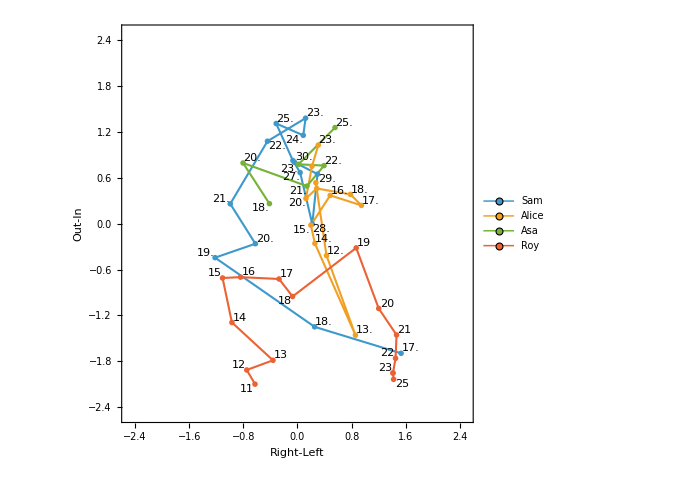

```mathematica
ListPlot[{Labeled[#[[1]],#[[2]]]&/@Transpose[{deviationPosSD[#]&/@samZ[[2;;]],samAgeM[[2;;]]}],Labeled[#[[1]],#[[2]]]&/@Transpose[{deviationPosSD[#]&/@aliceZ,aliceAgeM}],Labeled[#[[1]],#[[2]]]&/@Transpose[{deviationPosSD[#]&/@asaZ,asaAgeM}],Labeled[#[[1]],#[[2]]]&/@Transpose[{deviationPosSD[#]&/@debRoyMonth[[2;;]],debRoyAgeM[[2;;]]}]},Joined->True,Frame->True,AspectRatio->1,PlotMarkers->{Graphics[{Disk[]}],0.02},PlotStyle->Thickness[0.003],FrameLabel->{"Right-Left","Out-In"},FrameStyle->14,ImageSize->500,PlotLegends->{"Sam","Alice","Asa","Roy"},PlotRange->{{-2.5,2.5},{-2.5,2.5}}]
```

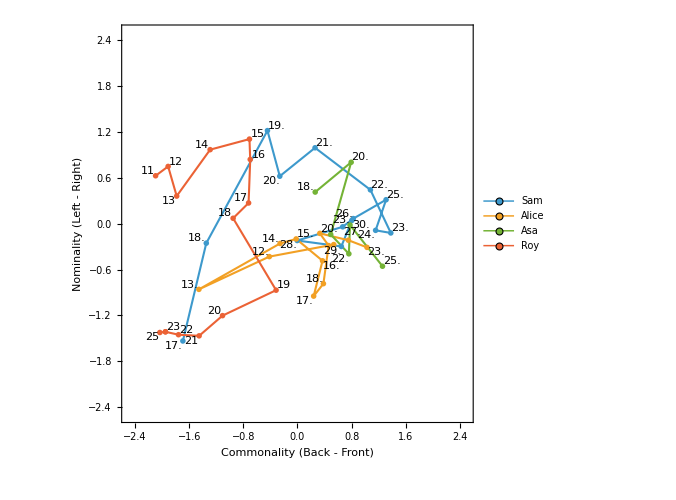

```mathematica
ListPlot[{Labeled[#[[1]],#[[2]]]&/@Transpose[{deviationPosPaper[#]&/@samZ[[2;;]],samAgeM[[2;;]]}],Labeled[#[[1]],#[[2]]]&/@Transpose[{deviationPosPaper[#]&/@aliceZ,aliceAgeM}],Labeled[#[[1]],#[[2]]]&/@Transpose[{deviationPosPaper[#]&/@asaZ,asaAgeM}],Labeled[#[[1]],#[[2]]]&/@Transpose[{deviationPosPaper[#]&/@debRoyMonth[[2;;]],debRoyAgeM[[2;;]]}]},Joined->True,Frame->True,AspectRatio->1,PlotMarkers->{Graphics[{Disk[]}],0.02},PlotStyle->Thickness[0.003],FrameLabel->{"Commonality (Back - Front)","Nominality (Left - Right)"},FrameStyle->14,ImageSize->500,PlotLegends->{"Sam","Alice","Asa","Roy"},PlotRange->{{-2.5,2.5},{-2.5,2.5}}]
```

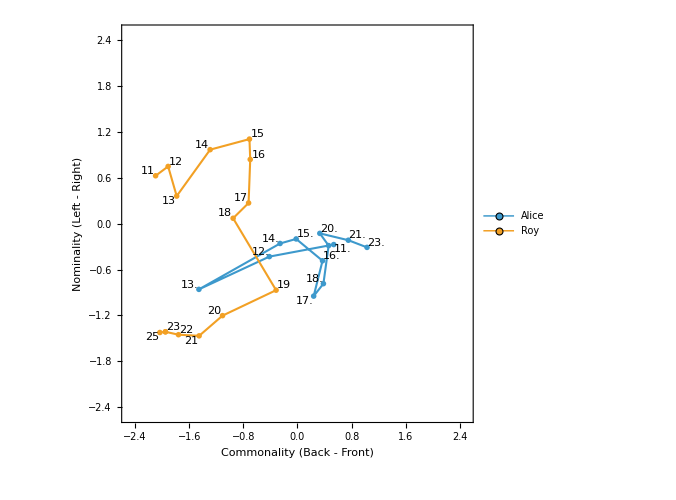

```mathematica
ListPlot[{Labeled[#[[1]],#[[2]]]&/@Transpose[{deviationPosPaper[#]&/@aliceZ,aliceAgeM}],Labeled[#[[1]],#[[2]]]&/@Transpose[{deviationPosPaper[#]&/@debRoyMonth[[2;;]],debRoyAgeM[[2;;]]}]},Joined->True,Frame->True,AspectRatio->1,PlotMarkers->{Graphics[{Disk[]}],0.02},PlotStyle->Thickness[0.003],FrameLabel->{"Commonality (Back - Front)","Nominality (Left - Right)"},FrameStyle->14,ImageSize->500,PlotLegends->{"Alice","Roy"},PlotRange->{{-2.5,2.5},{-2.5,2.5}}]
```

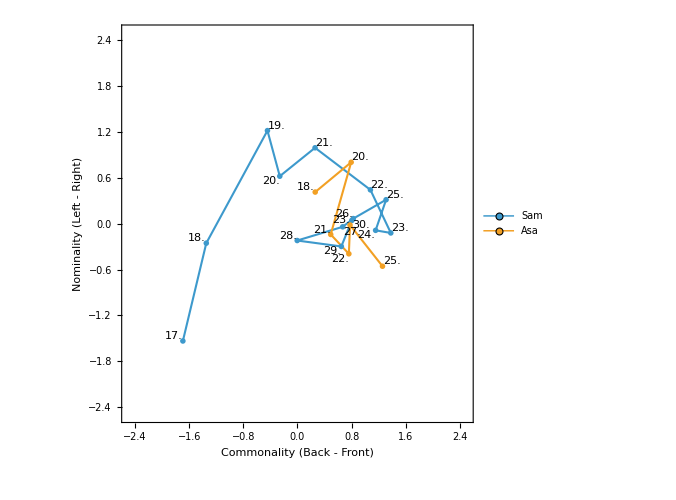

```mathematica
ListPlot[{Labeled[#[[1]],#[[2]]]&/@Transpose[{deviationPosPaper[#]&/@samZ[[2;;]],samAgeM[[2;;]]}],Labeled[#[[1]],#[[2]]]&/@Transpose[{deviationPosPaper[#]&/@asaZ,asaAgeM}]},Joined->True,Frame->True,AspectRatio->1,PlotMarkers->{Graphics[{Disk[]}],0.02},PlotStyle->Thickness[0.003],FrameLabel->{"Commonality (Back - Front)","Nominality (Left - Right)"},FrameStyle->14,ImageSize->500,PlotLegends->{"Sam","Asa"},PlotRange->{{-2.5,2.5},{-2.5,2.5}}]
```

```mathematica
(*四児の月齢と，SD単位のRight–Left／Out–In座標を表にまとめる．
Assemble the four children's ages and SD-scaled Right–Left/Out–In coordinates into a table.*)childTrajectoriesForExport=<|"Sam"->{samAgeM[[2;;]],samZ[[2;;]]},"Asa"->{asaAgeM,asaZ},"Alice"->{aliceAgeM,aliceZ},"Roy"->{debRoyAgeM[[2;;]],debRoyMonth[[2;;]]}|>;

workoutputSD=Prepend[Flatten[KeyValueMap[Function[{child,ageAndZ},MapThread[Join[{child,#1},deviationPosSD[#2]]&,ageAndZ]],childTrajectoriesForExport],1],{"name","AgeM","Right-Left","Out-In"}];
```

```mathematica
Grid[workoutputSD,Frame->All]
```

name | AgeM | Right-Left | Out-In
Sam | 17. | 1.5336 | -1.69474
Sam | 18. | 0.253886 | -1.34842
Sam | 19. | -1.21839 | -0.44367
Sam | 20. | -0.62197 | -0.261228
Sam | 21. | -0.993854 | 0.260691
Sam | 22. | -0.443488 | 1.07947
Sam | 23. | 0.120358 | 1.38126
Sam | 24. | 0.0861628 | 1.15642
Sam | 25. | -0.314298 | 1.31135
Sam | 26. | -0.0674784 | 0.826588
Sam | 27. | 0.0400375 | 0.669625
Sam | 28. | 0.219502 | -0.00347437
Sam | 29. | 0.297026 | 0.649262
Sam | 30. | -0.0429386 | 0.80407
Asa | 18. | -0.414535 | 0.262819
Asa | 20. | -0.80448 | 0.794831
Asa | 21. | 0.139998 | 0.492216
Asa | 22. | 0.39314 | 0.760631
Asa | 23. | 0.016265 | 0.777866
Asa | 25. | 0.555855 | 1.25817
Alice | 11. | 0.27225 | 0.537048
Alice | 12. | 0.429956 | -0.415558
Alice | 13. | 0.858295 | -1.45756
Alice | 14. | 0.258146 | -0.256989
Alice | 15. | 0.198653 | -0.0188449
Alice | 16. | 0.484291 | 0.371165
Alice | 17. | 0.946733 | 0.24005
Alice | 18. | 0.783793 | 0.384209
Alice | 19. | 0.285613 | 0.461456
Alice | 20. | 0.125771 | 0.331101
Alice | 21. | 0.215457 | 0.75311
Alice | 23. | 0.309078 | 1.02934
Roy | 11 | -0.627741 | -2.09825
Roy | 12 | -0.74979 | -1.9128
Roy | 13 | -0.361821 | -1.78629
Roy | 14 | -0.969205 | -1.29151
Roy | 15 | -1.10745 | -0.709707
Roy | 16 | -0.841234 | -0.698452
Roy | 17 | -0.271848 | -0.722598
Roy | 18 | -0.0717468 | -0.951523
Roy | 19 | 0.869049 | -0.315705
Roy | 20 | 1.20219 | -1.10845
Roy | 21 | 1.46634 | -1.45435
Roy | 22 | 1.45139 | -1.75965
Roy | 23 | 1.41341 | -1.95268
Roy | 24 | 1.41341 | -1.95268
Roy | 25 | 1.42255 | -2.03549

```mathematica
(* Export["RightLeftOutIn_SD_data_20261101.csv",workoutputSD];*)
```